```mathematica
AppendTo[$Path,"~/projects/KnotTheory/trunk/"];
AppendTo[$Path,"~/projects/KnotTheory/"];
```

```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of January 20, 2015, 10:42:19.1122.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
<<QuantumGroups`
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Remember to set QuantumGroupsDataDirectory[] to the appropriate path, if you've downloaded precomputed data.

```mathematica
brace[l_]:=brace[0,l]
brace[k_,l_]:=w^k v^l+w^-k v^-l
bracket[k_,l_]:=w^k v^l-w^-k v^-l
```

```mathematica
dw=-(brace[2]bracket[1,5]bracket[1,-6])/(bracket[1,0]bracket[1,-1]);
```

```mathematica
Clear[i]
```

```mathematica
i[X_Times]:=i/@X
i[Power[X_,k_]]:=i[X]^k
i[n_Integer]:=n
```

```mathematica
i[1-x_]:=-i[x-1]
i[v]=v;
i[w]=w;
i[q]=q;
i[X_Plus]/;X⟦1⟧=!=1∧X⟦1⟧=!=-1:=X⟦1⟧i[Expand[X/X⟦1⟧]]
```

```mathematica
c[n_,z_]:=
With[{a=Exponent[z,v],b=Exponent[z,w]},
Product[(PowerExpand[(v^a w^b)^(n/(2d))]brk[(n b)/(2 d),(n a)/(2d)])^MoebiusMu[d],{d,Divisors[n]}]
]
```

```mathematica
cq[n_]:=
Product[(q^(n/(2d))qi[n/(2d)])^MoebiusMu[d],{d,Divisors[n]}]
```

```mathematica
Do[i[Cyclotomic[n,z]]=c[n,z],{n,1,20},{z,DeleteCases[Flatten[Table[v^k w^l,{k,-12,12},{l,-6,6}]],1]}];
```

```mathematica
Do[i[Cyclotomic[n,z]]=c[n,z],{n,1,20},{z,DeleteCases[Table[v^k,{k,-50,50}],1]}];
```

```mathematica
Do[i[Cyclotomic[n,q]]=cq[n],{n,1,100}]
```

KnotTheory::loading: Loading precomputed data in PD4Knots`.

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

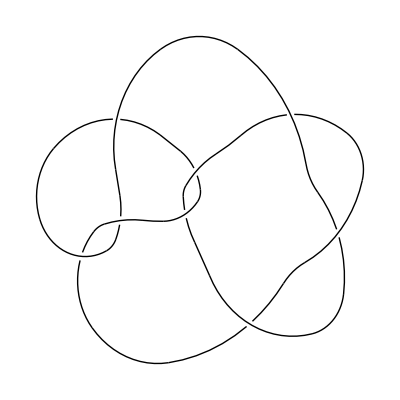

```mathematica
DrawPD[Knot[8,19]]
```

```mathematica
Writhe[k:(_Knot|_Link|_BR)]:=Writhe[PD[k]]
Writhe[p_PD]:=With[{o=OPD[p]},Count[o,_Xp]-Count[o,_Xn]]
```

```mathematica
RotateBox[X_,0]:=X
RotateBox[RotateBox[X_,k_],l_]:=RotateBox[X,k+l]
```

```mathematica
ClearAll[PlanarDiagram]
```

```mathematica
SetAttributes[PlanarDiagram,{Flat,Orderless,OneIdentity}]
```

```mathematica
PlanarDiagram[Box[{a_,a_,b___},X_]]:=PlanarDiagram[Box[{b},Stitch[X]]]
PlanarDiagram[Box[{a__,b_,b_,c___},X_]]:=PlanarDiagram[Box[{b,b,c,a},RotateBox[X,Length[{a}]]]]
```

```mathematica
PlanarDiagram[Box[{b_,c_,d_},X_],Box[{d_,c_,e___},Y_]]:=PlanarDiagram[Box[{b,e},Multiply[2][X,Y]]]
PlanarDiagram[Box[{a_,b_,c_,d_},X_],Box[{d_,c_,e___},Y_]]:=PlanarDiagram[Box[{a,b,e},Multiply[2][X,Y]]]
PlanarDiagram[Box[{a___,b_,c_,d___},X_],Box[{e___,c_,b_,f___},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,f,e},RotateBox[Y,Length[{e}]]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{d___,a_,c_,e___},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,e,d},RotateBox[Y,Length[{d}]]]]
PlanarDiagram[Box[{a___,b_,c_,d__},X_],Box[{b_,e___,c_},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,e},RotateBox[Y,-1]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{c_,d___,a_},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,d},RotateBox[Y,-1]]]
```

```mathematica
PlanarDiagram[Box[{a___,b_,c___},X_],Box[{d___,b_,e___},Y_]]:=PlanarDiagram[Box[{c,a,e,d},Multiply[1][RotateBox[X,-Length[{c}]],RotateBox[Y,Length[{d}]]]]]
```

```mathematica
PlanarDiagram[p_PD]:=PlanarDiagram@@(p/.{X[a_,b_,c_,d_]:>Box[{c,d,a,b},X],Y[a_,b_,c_]:>Box[{a,b,c},Y]})
```

```mathematica
PlanarDiagram[K:(_Knot|_Link)]:=Module[{result},
result=Quiet[PlanarDiagram[PD[K]],$IterationLimit::itlim];
If[FreeQ[result,Hold],
PlanarDiagram[K]=result,
$Failed]
]
```

```mathematica
PlanarDiagram[Knot[8,19]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][X,Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-1]],1]]],1]]]]]

```mathematica
Cases[AllKnots[{3,11}],K_/;PlanarDiagram[K]⟦1,1⟧≠{}]
```

KnotTheory::loading: Loading precomputed data in DTCode4KnotsTo11`.

KnotTheory::credits: The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005.

{}

```mathematica
Cases[AllKnots[12],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

{Knot[12,Alternating,887],Knot[12,Alternating,888],Knot[12,NonAlternating,703]}

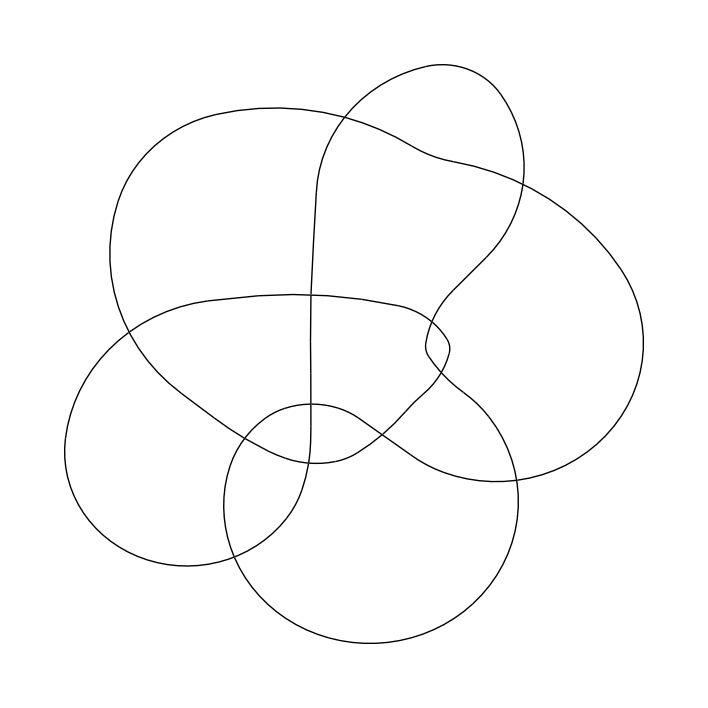

```mathematica
DrawPD[Knot[12,Alternating,887]]
```

### Loading matrices

```mathematica
Clear[QESRotation,QESBraiding,QESInverseBraiding,QESCupCap,QESCap,QESCup,QESI,QESH,QESFork,QESFuse]
```

```mathematica
ZeroMatrix[n_]:=Table[0,{n},{n}]
ZeroMatrix[n_,m_]:=Table[0,{n},{m}]
```

```mathematica
QESDimension[n_]:=Length[QESRotation[n]]
```

```mathematica
QESId[n_]:=IdentityMatrix[QESDimension[n]]
QESZero[n_,m_]:=ZeroMatrix[QESDimension[n],QESDimension[m]]
QESRotation[0]:={{1}}
QESRotation[1]:={}
QESRotation[n_]:=QESRotation[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-rotation-matrix.m"}]];
QESRotation[n_,k_]/;k<0∨k≥n:=QESRotation[n,Mod[k,n]]
QESRotation[n_,0]:=IdentityMatrix[Length[QESRotation[n]]]
QESRotation[n_,1]:=QESRotation[n]
QESRotation[n_,k_]:=QESRotation[n,k]=Together[QESRotation[n].QESRotation[n,k-1]]
QESBraiding[n_]:=QESBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-braiding-matrix.m"}]];
QESBraiding[n_,k_]:=QESBraiding[n,k]=Together[QESRotation[n,-k].QESBraiding[n].QESRotation[n,k]]
QESInverseBraiding[n_]:=QESInverseBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-inverse-braiding-matrix.m"}]];
QESInverseBraiding[n_,k_]:=QESInverseBraiding[n,k]=Together[QESRotation[n,-k].QESInverseBraiding[n].QESRotation[n,k]]
QESCupCap[n_]:=QESCupCap[n]=Together[QESCup[n-2].QESCap[n]]
QESCupCap[3]={{0}};
QESCup[0]={{1}};
QESCup[1]={{}};
QESCup[n_]:=QESCup[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cup-matrix.m"}]]
QESCap[2]={{d}};
QESCap[n_]:=QESCap[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cap-matrix.m"}]]
QESI[n_]:=QESI[n]=Together[QESFork[n-1].QESFuse[n]]
QESFork[n_]:=QESFork[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fork-matrix.m"}]]
QESFuse[n_]:=QESFuse[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fuse-matrix.m"}]]
QESH[n_]:=QESH[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-H-matrix.m"}]]
```

### Verifying matrices

```mathematica
Table[Together[QESRotation[k,k-1].QESRotation[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESCupCap[k].QESCupCap[k]==d QESCupCap[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESFuse[k+2].QESCup[k]==QESZero[k+1,k],{k,1,4}]
```

{True,True,True,True}

```mathematica
Table[Together[QESBraiding[k].QESInverseBraiding[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[Together[QESInverseBraiding[k].QESBraiding[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESBraiding[k+1].QESFork[k]==(-v^6)QESFork[k],{k,2,5}]
```

{True,True,True,True}

```mathematica
Table[QESInverseBraiding[k+1].QESFork[k]==(-v^-6)QESFork[k],{k,2,5}]
```

{True,True,True,True}

```mathematica
Table[QESBraiding[k+2].QESCup[k]==(v^12)QESCup[k],{k,2,4}]
```

{True,True,True}

```mathematica
Table[QESInverseBraiding[k+2].QESCup[k]==(v^-12)QESCup[k],{k,2,4}]
```

{True,True,True}

```mathematica
(*Table[Together[QESBraiding[k,0].QESBraiding[k,1].QESBraiding[k,0]-QESBraiding[k,1].QESBraiding[k,0].QESBraiding[k,1]]==QESZero[k],{k,2,6}]*)
```

```mathematica
(* There's still lots more interesting stuff that could be verified here. *)
```

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESCupCap[k]/.d->dw],{k,2,6}]]]]
```

-(v^33 w^4 brk[0,1] brk[0,3] brk[0,6] brk[1,-1] brk[1,0] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^2)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESI[k],{k,3,6}]]]
```

v^18 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4)^2 (1+d v^2+v^4) (1+d v^8+v^16)^3

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESI[k]/.d->dw],{k,3,6}]]]]
```

(v^40 w^2 brk[0,3]^2 brk[0,6] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^3)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESH[k],{k,3,6}]]]
```

v^16 (1+v^2) (1-v+v^2)^2 (1+v+v^2)^2 (1+v^4)^2 (1+d v^2+v^4) (1+d v^8+v^16)^4

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESH[k]/.d->dw],{k,3,6}]]]]
```

(v^48 w^2 brk[0,1] brk[0,3]^3 brk[0,6] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^4)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESBraiding[k],{k,3,6}]]]
```

v^24 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^2+v^4)^2 (1+d v^8+v^16)^3

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESBraiding[k]/.d->dw],{k,3,6}]]]]
```

(v^43 w^4 brk[0,1]^2 brk[0,3] brk[0,6]^2 i[1+w^2/v^6+v^4 w^2+w^4/v^2]^3)/brk[0,2]^2

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESInverseBraiding[k],{k,3,6}]]]
```

v^30 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^2+v^4)^2 (1+d v^8+v^16)^3

### Stuff

```mathematica
RotateBox[QESBox[n_][v_],k_]:=QESBox[n][Together[QESRotation[n,k].v]]
```

```mathematica
Stitch[QESBox[n_][v_]]:=QESBox[n-2][Together[QESCap[n].v]]
Stitch[QESBox[3][v_]]:=QESBox[1][{}]
```

```mathematica
AddStrand[QESBox[n_][v_]]:=QESBox[n+2][Together[QESCup[n].v]]
```

```mathematica
Multiply[2][QESBox[4][w_],QESBox[n_][v_]]:=QESBox[n][Together[Together[w.{QESCupCap[n],IdentityMatrix[Length[v]],QESI[n],QESH[n],QESBraiding[n]}].v]]
```

```mathematica
Multiply[2][QESBox[3][w_],QESBox[n_][v_]]:=QESBox[n-1][Together[Together[w.{QESFuse[n]}].v]]
```

```mathematica
Multiply[1][b1:QESBox[n1_][w_],b2:QESBox[n2_][v_]]:=Multiply[2][b1,RotateBox[AddStrand[RotateBox[b2,1]],-1]]
```

```mathematica
Multiply[1][QESBox[4][{1,0,0,0,0}],QESBox[4][{1,0,0,0,0}]]
```

QESBox[6][{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]

```mathematica
PlanarDiagram[unlink=PD[X[1,3,2,4],X[2,3,1,4]]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[X,1],RotateBox[X,-2]],1]]]]]

```mathematica
OPD[PD[crossings___]]:=OPD[crossings]/.{X[i_,j_,k_,l_]/;(j-l==1||l-j>1):>Xp[i,j,k,l],X[i_,j_,k_,l_]/;(l-j==1||j-l>1):>Xn[i,j,k,l]}
```

```mathematica
OPD[K_Knot]:=OPD[PD[K]]
OPD[L_Link]:=OPD[PD[L]]
```

```mathematica
PD[OPD[f___]]:=Module[{pairs,rules,n=0,cycles},
pairs = Unordered@@(Join@@({f}/.{Xp[i_,j_,k_,l_]:>{{i,k},{l,j}},Xn[i_,j_,k_,l_]:>{{i,k},{j,l}}}));
cycles=List@@(pairs//.Unordered[{x___,y_},{y_,z___}]:>Unordered[{x,y,z}]);
rules=#->++n&/@Flatten[cycles];
PD[f]/.rules/.{Xp|Xn->X}
]
```

```mathematica
Clear[QESInvariant]
```

```mathematica
QESInvariant[K:(_Knot|_Link|_PD|_OPD)]:=v^(-12 Writhe[K])QESInvariant[PlanarDiagram[K]]
QESInvariant[planarDiagram_PlanarDiagram]:=QESInvariant[planarDiagram]=(planarDiagram/.{X->QESBox[4][QESBraiding[4]⟦All,2⟧],Y->QESBox[3][{1}]})/.PlanarDiagram[Box[{},QESBox[0][{z_}]]]:>Together[z]
```

```mathematica
timesToList[X_Times]:=List@@X
timesToList[X_]:={X}
```

```mathematica
Φ[brk[0,k_]]:=Product[Φ[d],{d,Cases[Divisors[k],d_/;Mod[d,4]≠2]}]
```

```mathematica
QESInvariantΦ[K_]:=Times@@(timesToList[i[Factor[QESInvariant[K]/.d->dw]]]/.i[t_]:>Collect[t,w,i[Factor[#]]&]/.i[t_]:>t/.brk[0,k_]:>Φ[brk[0,k]])
```

```mathematica
i41=Factor[QESInvariant[PD[Knot[4,1]]]/.d->dw]
```

-1/(v^36 (v-w) (-1+w) w^6 (1+w) (v+w))(1+v^4) (v^6-w) (v^6+w) (-1+v^5 w) (1+v^5 w) (v^16-v^26-v^28+v^38+v^4 w^2-v^8 w^2+v^12 w^2-2 v^14 w^2-2 v^16 w^2+2 v^18 w^2+v^20 w^2-2 v^22 w^2+4 v^26 w^2-2 v^30 w^2+v^32 w^2+2 v^34 w^2-2 v^36 w^2-2 v^38 w^2+v^40 w^2-v^44 w^2+v^48 w^2-v^2 w^4-v^4 w^4+2 v^6 w^4-3 v^10 w^4+v^12 w^4+6 v^14 w^4-v^16 w^4-5 v^18 w^4+3 v^20 w^4+5 v^22 w^4-6 v^24 w^4-6 v^26 w^4+5 v^28 w^4+3 v^30 w^4-5 v^32 w^4-v^34 w^4+6 v^36 w^4+v^38 w^4-3 v^40 w^4+2 v^44 w^4-v^46 w^4-v^48 w^4+w^6+2 v^2 w^6-v^4 w^6-2 v^6 w^6+2 v^8 w^6+2 v^10 w^6-6 v^12 w^6-4 v^14 w^6+7 v^16 w^6+2 v^18 w^6-8 v^20 w^6+11 v^24 w^6-8 v^28 w^6+2 v^30 w^6+7 v^32 w^6-4 v^34 w^6-6 v^36 w^6+2 v^38 w^6+2 v^40 w^6-2 v^42 w^6-v^44 w^6+2 v^46 w^6+v^48 w^6-w^8-v^2 w^8+2 v^4 w^8-3 v^8 w^8+v^10 w^8+6 v^12 w^8-v^14 w^8-5 v^16 w^8+3 v^18 w^8+5 v^20 w^8-6 v^22 w^8-6 v^24 w^8+5 v^26 w^8+3 v^28 w^8-5 v^30 w^8-v^32 w^8+6 v^34 w^8+v^36 w^8-3 v^38 w^8+2 v^42 w^8-v^44 w^8-v^46 w^8+w^10-v^4 w^10+v^8 w^10-2 v^10 w^10-2 v^12 w^10+2 v^14 w^10+v^16 w^10-2 v^18 w^10+4 v^22 w^10-2 v^26 w^10+v^28 w^10+2 v^30 w^10-2 v^32 w^10-2 v^34 w^10+v^36 w^10-v^40 w^10+v^44 w^10+v^10 w^12-v^20 w^12-v^22 w^12+v^32 w^12)

```mathematica
Factor[(i41/.w->v/w)-i41]
```

0

```mathematica
qi[q_,m_]:=Sum[q^k,{k,-m+1,m-1,2}]
```

```mathematica
Factor[QESInvariant[PD[Knot[3,1]]]/.d->dw]
```

1/((v-w) (-1+w) w^4 (1+w) (v+w))v^12 (1+v^4) (v^6-w) (v^6+w) (-1+v^5 w) (1+v^5 w) (-v^4+v^14+v^16-v^26-v^6 w^2+v^10 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2+v^26 w^2-v^28 w^2+v^32 w^2-v^36 w^2-w^4-v^2 w^4-v^8 w^4+2 v^12 w^4+v^14 w^4-v^16 w^4+2 v^20 w^4-v^22 w^4-3 v^24 w^4+v^28 w^4-v^32 w^4+v^34 w^4+v^36 w^4-v^4 w^6+v^8 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6+v^24 w^6-v^26 w^6+v^30 w^6-v^34 w^6-w^8+v^10 w^8+v^12 w^8-v^22 w^8)

```mathematica
Collect[1/w^4(-v^4+v^14+v^16-v^26-v^6 w^2+v^10 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2+v^26 w^2-v^28 w^2+v^32 w^2-v^36 w^2-w^4-v^2 w^4-v^8 w^4+2 v^12 w^4+v^14 w^4-v^16 w^4+2 v^20 w^4-v^22 w^4-3 v^24 w^4+v^28 w^4-v^32 w^4+v^34 w^4+v^36 w^4-v^4 w^6+v^8 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6+v^24 w^6-v^26 w^6+v^30 w^6-v^34 w^6-w^8+v^10 w^8+v^12 w^8-v^22 w^8),w,Collect[#,v]&]
```

-1-v^2-v^8+2 v^12+v^14-v^16+2 v^20-v^22-3 v^24+v^28-v^32+v^34+v^36+(-v^4+v^14+v^16-v^26)/w^4+(-v^6+v^10-v^14+v^16+v^18-v^20-v^22+v^24+v^26-v^28+v^32-v^36)/w^2+(-v^4+v^8-v^12+v^14+v^16-v^18-v^20+v^22+v^24-v^26+v^30-v^34) w^2+(-1+v^10+v^12-v^22) w^4

```mathematica
(w^4+v^4 w^-4)(-1+v^10+v^12-v^22)+(w^2+v^2 w^-2)(-v^4+v^8-v^12+v^14+v^16-v^18-v^20+v^22+v^24-v^26+v^30-v^34)+(-1-v^2-v^8+2 v^12+v^14-v^16+2 v^20-v^22-3 v^24+v^28-v^32+v^34+v^36)//TeXForm
```

v^{36}+v^{34}-v^{32}+v^{28}-3 v^{24}-v^{22}+2 v^{20}-v^{16}+v^{14}+2 v^{12}-v^8-v^2+\left(-v^{22}+v^{12}+v^{10}-1\right)
   \left(\frac{v^4}{w^4}+w^4\right)+\left(-v^{34}+v^{30}-v^{26}+v^{24}+v^{22}-v^{20}-v^{18}+v^{16}+v^{14}-v^{12}+v^8-v^4\right) \left(\frac{v^2}{w^2}+w^2\right)-1

```mathematica
QESInvariantΦ[PD[Knot[4,1]]]
```

-1/(v^8 w^6 brk[1,-1] brk[1,0])brk[1,-6] brk[1,5] Φ[4] (((1+2 v^2-v^4-2 v^6+2 v^8+2 v^10-6 v^12-4 v^14+7 v^16+2 v^18-8 v^20+11 v^24-8 v^28+2 v^30+7 v^32-4 v^34-6 v^36+2 v^38+2 v^40-2 v^42-v^44+2 v^46+v^48) w^6)/v^16+v^11 Φ[1]^2 Φ[3] Φ[5]-((1+v^2-2 v^4+3 v^8-4 v^12+3 v^16-2 v^20+v^22+v^24) w^4 Φ[1]^2 Φ[3] Φ[5])/v^3-((1+v^2-2 v^4+3 v^8-4 v^12+3 v^16-2 v^20+v^22+v^24) w^8 Φ[1]^2 Φ[3] Φ[5])/v^5+v^5 w^12 Φ[1]^2 Φ[3] Φ[5]+v^10 w^2 Φ[1]^4 Φ[3] Φ[5]^2 Φ[8]+v^6 w^10 Φ[1]^4 Φ[3] Φ[5]^2 Φ[8])

```mathematica
Cyclotomic[5,x]
```

1+x+x^2+x^3+x^4

```mathematica
Φv[k_]/;OddQ[k]:=v^(-EulerPhi[k])Cyclotomic[k,v]Cyclotomic[2k,v]
Φv[k_]/;Mod[k,4]==0:=v^(-EulerPhi[k]/2)Cyclotomic[k,v]
```

```mathematica
Collect[Φv[5],v]
```

1+1/v^4+1/v^2+v^2+v^4

```mathematica
Collect[Φv[4],v]
```

1/v+v

```mathematica
QESInvariant[PD[ArcPresentation[{3,5},{6,4},{5,2},{1,3},{2,6},{4,1}]]]
```

1/(v^44 (1+d v^2+v^4)^3)d (2+d v^2+5 v^4+d v^6+4 v^8-4 v^10-2 v^12+d v^12-8 v^14+2 d v^14+d^2 v^14-9 v^16+6 d v^16+d^2 v^16-5 v^18+2 d v^18+d^2 v^18-6 v^20+3 d v^20-d^2 v^20+6 v^22-2 d v^22-d^2 v^22+3 v^24-12 d v^24+2 d^2 v^24+19 v^26-10 d v^26-2 d^2 v^26+d^3 v^26+7 v^28-20 d v^28+5 d^2 v^28+16 v^30-7 d v^30+2 d^2 v^30-v^32-8 d v^32+2 d^2 v^32+12 d v^34-3 d^2 v^34-d^3 v^34-14 v^36+17 d v^36-5 d^2 v^36-d^3 v^36-16 v^38+30 d v^38-9 d^2 v^38-11 v^40+24 d v^40-8 d^2 v^40+d^3 v^40-15 v^42+18 d v^42-6 d^2 v^42+d^3 v^42+4 v^44+5 d v^44-d^2 v^44+2 v^46-21 d v^46+7 d^2 v^46+22 v^48-16 d v^48+8 d^2 v^48+10 v^50-40 d v^50+20 d^2 v^50-d^3 v^50+22 v^52-16 d v^52+8 d^2 v^52+2 v^54-21 d v^54+7 d^2 v^54+4 v^56+5 d v^56-d^2 v^56-15 v^58+18 d v^58-6 d^2 v^58+d^3 v^58-11 v^60+24 d v^60-8 d^2 v^60+d^3 v^60-16 v^62+30 d v^62-9 d^2 v^62-14 v^64+17 d v^64-5 d^2 v^64-d^3 v^64+12 d v^66-3 d^2 v^66-d^3 v^66-v^68-8 d v^68+2 d^2 v^68+16 v^70-7 d v^70+2 d^2 v^70+7 v^72-20 d v^72+5 d^2 v^72+19 v^74-10 d v^74-2 d^2 v^74+d^3 v^74+3 v^76-12 d v^76+2 d^2 v^76+6 v^78-2 d v^78-d^2 v^78-6 v^80+3 d v^80-d^2 v^80-5 v^82+2 d v^82+d^2 v^82-9 v^84+6 d v^84+d^2 v^84-8 v^86+2 d v^86+d^2 v^86-2 v^88+d v^88-4 v^90+4 v^92+d v^94+5 v^96+d v^98+2 v^100)

```mathematica
(*DeleteFile[FileNameJoin[{NotebookDirectory[],"QES-Knot-Polynomials.m"}]]*)
```

```mathematica
With[{file=FileNameJoin[{NotebookDirectory[],"QES-Knot-Polynomials.m"}]},
If[FileExistsQ[file],
DownValues[QESInvariant]=Get[file]~Join~DownValues[QESInvariant]
]
];
```

```mathematica
QESInvariant[unlink]
```

d^2 v^24

```mathematica
QESInvariant[Knot[3,1]]
```

-1/((1+d v^2+v^4)^2)d v^4 (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+5 d v^28-2 d^2 v^28-2 v^30-d^2 v^30+v^34-6 d v^34+2 d^2 v^34+v^36-5 d v^36+2 d^2 v^36+3 v^38-6 d v^38+2 d^2 v^38+v^40-5 d v^40+2 d^2 v^40+v^42+2 d v^42-v^44-v^46+6 d v^46-2 d^2 v^46-6 v^48+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74)

```mathematica
Factor[%/.d->dw]
```

1/((v-w) (-1+w) w^4 (1+w) (v+w))v^12 (1+v^4) (v^6-w) (v^6+w) (-1+v^5 w) (1+v^5 w) (-v^4+v^14+v^16-v^26-v^6 w^2+v^10 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2+v^26 w^2-v^28 w^2+v^32 w^2-v^36 w^2-w^4-v^2 w^4-v^8 w^4+2 v^12 w^4+v^14 w^4-v^16 w^4+2 v^20 w^4-v^22 w^4-3 v^24 w^4+v^28 w^4-v^32 w^4+v^34 w^4+v^36 w^4-v^4 w^6+v^8 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6+v^24 w^6-v^26 w^6+v^30 w^6-v^34 w^6-w^8+v^10 w^8+v^12 w^8-v^22 w^8)

```mathematica
i[%]
```

-1/(w^4 brk[0,2] brk[1,-1] brk[1,0])v^28 brk[0,4] brk[1,-6] brk[1,5] i[1-v^10-v^12+v^22+v^2 w^2-v^6 w^2+v^10 w^2-v^12 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2-v^28 w^2+v^32 w^2+w^4/v^4+w^4/v^2+v^4 w^4-2 v^8 w^4-v^10 w^4+v^12 w^4-2 v^16 w^4+v^18 w^4+3 v^20 w^4-v^24 w^4+v^28 w^4-v^30 w^4-v^32 w^4+w^6-v^4 w^6+v^8 w^6-v^10 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6-v^26 w^6+v^30 w^6+w^8/v^4-v^6 w^8-v^8 w^8+v^18 w^8]

```mathematica
Collect[(1/(v^8 w^4))(1-v^10-v^12+v^22+v^2 w^2-v^6 w^2+v^10 w^2-v^12 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2-v^28 w^2+v^32 w^2+w^4/v^4+w^4/v^2+v^4 w^4-2 v^8 w^4-v^10 w^4+v^12 w^4-2 v^16 w^4+v^18 w^4+3 v^20 w^4-v^24 w^4+v^28 w^4-v^30 w^4-v^32 w^4+w^6-v^4 w^6+v^8 w^6-v^10 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6-v^26 w^6+v^30 w^6+w^8/v^4-v^6 w^8-v^8 w^8+v^18 w^8),w,Factor]
```

-(-1-v^2-v^8+2 v^12+v^14-v^16+2 v^20-v^22-3 v^24+v^28-v^32+v^34+v^36)/v^12+((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4))/(v^8 w^4)+((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4) (1-v^4+v^8))/(v^6 w^2)+((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4) (1-v^4+v^8) w^2)/v^8+((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4) w^4)/v^12

```mathematica
Φ[brk[0,12]]
```

Φ[1] Φ[3] Φ[4] Φ[12]

```mathematica
Collect[(1/(v^8 w^4))(1-v^10-v^12+v^22+v^2 w^2-v^6 w^2+v^10 w^2-v^12 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2-v^28 w^2+v^32 w^2+w^4/v^4+w^4/v^2+v^4 w^4-2 v^8 w^4-v^10 w^4+v^12 w^4-2 v^16 w^4+v^18 w^4+3 v^20 w^4-v^24 w^4+v^28 w^4-v^30 w^4-v^32 w^4+w^6-v^4 w^6+v^8 w^6-v^10 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6-v^26 w^6+v^30 w^6+w^8/v^4-v^6 w^8-v^8 w^8+v^18 w^8),w,i[Factor[#]]/.brk[0,k_]:>Φ[brk[0,k]]&]
```

-i[-1-v^2-v^8+2 v^12+v^14-v^16+2 v^20-v^22-3 v^24+v^28-v^32+v^34+v^36]/v^12+(v^3 Φ[1]^2 Φ[3] Φ[5])/w^4+(w^4 Φ[1]^2 Φ[3] Φ[5])/v+(v^9 Φ[1]^2 Φ[3] Φ[5] Φ[12])/w^2+v^7 w^2 Φ[1]^2 Φ[3] Φ[5] Φ[12]

```mathematica
QESInvariant[Knot[4,1]]
```

1/(v^44 (1+d v^2+v^4)^3)d (2+d v^2+5 v^4+d v^6+4 v^8-4 v^10-2 v^12+d v^12-8 v^14+2 d v^14+d^2 v^14-9 v^16+6 d v^16+d^2 v^16-5 v^18+2 d v^18+d^2 v^18-6 v^20+3 d v^20-d^2 v^20+6 v^22-2 d v^22-d^2 v^22+3 v^24-12 d v^24+2 d^2 v^24+19 v^26-10 d v^26-2 d^2 v^26+d^3 v^26+7 v^28-20 d v^28+5 d^2 v^28+16 v^30-7 d v^30+2 d^2 v^30-v^32-8 d v^32+2 d^2 v^32+12 d v^34-3 d^2 v^34-d^3 v^34-14 v^36+17 d v^36-5 d^2 v^36-d^3 v^36-16 v^38+30 d v^38-9 d^2 v^38-11 v^40+24 d v^40-8 d^2 v^40+d^3 v^40-15 v^42+18 d v^42-6 d^2 v^42+d^3 v^42+4 v^44+5 d v^44-d^2 v^44+2 v^46-21 d v^46+7 d^2 v^46+22 v^48-16 d v^48+8 d^2 v^48+10 v^50-40 d v^50+20 d^2 v^50-d^3 v^50+22 v^52-16 d v^52+8 d^2 v^52+2 v^54-21 d v^54+7 d^2 v^54+4 v^56+5 d v^56-d^2 v^56-15 v^58+18 d v^58-6 d^2 v^58+d^3 v^58-11 v^60+24 d v^60-8 d^2 v^60+d^3 v^60-16 v^62+30 d v^62-9 d^2 v^62-14 v^64+17 d v^64-5 d^2 v^64-d^3 v^64+12 d v^66-3 d^2 v^66-d^3 v^66-v^68-8 d v^68+2 d^2 v^68+16 v^70-7 d v^70+2 d^2 v^70+7 v^72-20 d v^72+5 d^2 v^72+19 v^74-10 d v^74-2 d^2 v^74+d^3 v^74+3 v^76-12 d v^76+2 d^2 v^76+6 v^78-2 d v^78-d^2 v^78-6 v^80+3 d v^80-d^2 v^80-5 v^82+2 d v^82+d^2 v^82-9 v^84+6 d v^84+d^2 v^84-8 v^86+2 d v^86+d^2 v^86-2 v^88+d v^88-4 v^90+4 v^92+d v^94+5 v^96+d v^98+2 v^100)

```mathematica
QESInvariant[Knot[8,19]]
```

1/(v^166 (1+d v^2+v^4)^6)d (1-v^2+5 v^4-d v^4-5 v^6-d v^6+10 v^8-3 d v^8-11 v^10-4 d v^10+d^2 v^10+10 v^12+4 d v^12-14 v^14-5 d v^14+3 d^2 v^14+4 v^16+25 d v^16-6 d^2 v^16-9 v^18-2 d v^18-5 d^2 v^18-3 v^20+36 d v^20-22 d^2 v^20+d^3 v^20+5 v^22-7 d v^22-18 d^2 v^22+4 d^3 v^22-3 v^24+5 d v^24-14 d^2 v^24+7 d^3 v^24+21 v^26-2 d v^26+6 d^2 v^26+8 d^3 v^26+11 v^28-67 d v^28+72 d^2 v^28-4 d^3 v^28+28 v^30+62 d v^30+62 d^2 v^30-8 d^3 v^30+29 v^32-110 d v^32+165 d^2 v^32-50 d^3 v^32+9 d^4 v^32+19 v^34+160 d v^34+77 d^2 v^34-42 d^3 v^34+10 d^4 v^34+d^5 v^34+26 v^36-60 d v^36+62 d^2 v^36-31 d^3 v^36+21 d^4 v^36-7 v^38+205 d v^38-6 d^2 v^38-13 d^3 v^38+20 d^4 v^38-3 v^40+22 d v^40-203 d^2 v^40+138 d^3 v^40-8 d^4 v^40-39 v^42+139 d v^42-131 d^2 v^42+136 d^3 v^42-28 d^4 v^42-28 v^44+29 d v^44-285 d^2 v^44+275 d^3 v^44-83 d^4 v^44+4 d^5 v^44-50 v^46-34 d v^46-88 d^2 v^46+200 d^3 v^46-109 d^4 v^46+10 d^5 v^46-24 v^48-38 d v^48+16 d^2 v^48+79 d^3 v^48-82 d^4 v^48+9 d^5 v^48-21 v^50-244 d v^50+153 d^2 v^50-70 d^3 v^50-39 d^4 v^50+12 d^5 v^50-d^6 v^50-7 v^52-63 d v^52+447 d^2 v^52-407 d^3 v^52+116 d^4 v^52-11 d^5 v^52+22 v^54-356 d v^54+248 d^2 v^54-429 d^3 v^54+220 d^4 v^54-28 d^5 v^54-5 v^56+21 d v^56+488 d^2 v^56-620 d^3 v^56+331 d^4 v^56-55 d^5 v^56+2 d^6 v^56+31 v^58-239 d v^58-126 d^2 v^58-304 d^3 v^58+330 d^4 v^58-73 d^5 v^58+4 d^6 v^58-20 v^60+159 d v^60+18 d^2 v^60-89 d^3 v^60+135 d^4 v^60-40 d^5 v^60+3 d^6 v^60+7 v^62+23 d v^62-732 d^2 v^62+410 d^3 v^62-31 d^4 v^62-19 d^5 v^62+3 d^6 v^62-36 v^64+237 d v^64-488 d^2 v^64+729 d^3 v^64-432 d^4 v^64+91 d^5 v^64-5 d^6 v^64-5 v^66+161 d v^66-812 d^2 v^66+932 d^3 v^66-561 d^4 v^66+133 d^5 v^66-8 d^6 v^66-37 v^68+124 d v^68-450 d^2 v^68+805 d^3 v^68-680 d^4 v^68+196 d^5 v^68-15 d^6 v^68+9 v^70+60 d v^70-54 d^2 v^70+376 d^3 v^70-482 d^4 v^70+163 d^5 v^70-14 d^6 v^70-16 v^72-165 d v^72+153 d^2 v^72-195 d^3 v^72-106 d^4 v^72+71 d^5 v^72-7 d^6 v^72+19 v^74-92 d v^74+927 d^2 v^74-866 d^3 v^74+312 d^4 v^74-58 d^5 v^74+5 d^6 v^74+13 v^76-376 d v^76+562 d^2 v^76-1261 d^3 v^76+816 d^4 v^76-216 d^5 v^76+19 d^6 v^76+7 v^78-54 d v^78+1153 d^2 v^78-1357 d^3 v^78+870 d^4 v^78-270 d^5 v^78+27 d^6 v^78+24 v^80-270 d v^80+136 d^2 v^80-1020 d^3 v^80+957 d^4 v^80-315 d^5 v^80+31 d^6 v^80-14 v^82+162 d v^82+334 d^2 v^82-326 d^3 v^82+349 d^4 v^82-153 d^5 v^82+16 d^6 v^82+15 v^84+38 d v^84-799 d^2 v^84+458 d^3 v^84+5 d^4 v^84-53 d^5 v^84+5 d^6 v^84-29 v^86+314 d v^86-661 d^2 v^86+1203 d^3 v^86-760 d^4 v^86+180 d^5 v^86-17 d^6 v^86+9 v^88+204 d v^88-1167 d^2 v^88+1619 d^3 v^88-997 d^4 v^88+258 d^5 v^88-25 d^6 v^88-29 v^90+182 d v^90-772 d^2 v^90+1422 d^3 v^90-1079 d^4 v^90+308 d^5 v^90-30 d^6 v^90+15 v^92+106 d v^92-385 d^2 v^92+1104 d^3 v^92-870 d^4 v^92+243 d^5 v^92-23 d^6 v^92-9 v^94-161 d v^94+48 d^2 v^94+37 d^3 v^94-190 d^4 v^94+80 d^5 v^94-10 d^6 v^94+20 v^96-52 d v^96+861 d^2 v^96-613 d^3 v^96+200 d^4 v^96-28 d^5 v^96-d^6 v^96+18 v^98-380 d v^98+729 d^2 v^98-1414 d^3 v^98+848 d^4 v^98-182 d^5 v^98+10 d^6 v^98+14 v^100-26 d v^100+1350 d^2 v^100-1597 d^3 v^100+863 d^4 v^100-189 d^5 v^100+11 d^6 v^100+29 v^102-261 d v^102+432 d^2 v^102-1331 d^3 v^102+900 d^4 v^102-198 d^5 v^102+11 d^6 v^102-v^104+182 d v^104+617 d^2 v^104-818 d^3 v^104+444 d^4 v^104-92 d^5 v^104+5 d^6 v^104+21 v^106+28 d v^106-490 d^2 v^106+132 d^3 v^106+100 d^4 v^106-43 d^5 v^106+5 d^6 v^106-19 v^108+333 d v^108-512 d^2 v^108+693 d^3 v^108-321 d^4 v^108+47 d^5 v^108+13 v^110+154 d v^110-1002 d^2 v^110+1280 d^3 v^110-520 d^4 v^110+67 d^5 v^110-29 v^112+220 d v^112-918 d^2 v^112+1199 d^3 v^112-509 d^4 v^112+67 d^5 v^112+16 v^114+44 d v^114-511 d^2 v^114+980 d^3 v^114-422 d^4 v^114+55 d^5 v^114-20 v^116-89 d v^116-344 d^2 v^116+410 d^3 v^116-153 d^4 v^116+25 d^5 v^116+19 v^118-85 d v^118+474 d^2 v^118-162 d^3 v^118-3 d^4 v^118+15 d^5 v^118-2 v^120-317 d v^120+437 d^2 v^120-478 d^3 v^120+148 d^4 v^120+10 v^122-52 d v^122+971 d^2 v^122-778 d^3 v^122+185 d^4 v^122+3 v^124-277 d v^124+554 d^2 v^124-551 d^3 v^124+151 d^4 v^124-4 v^126+110 d v^126+570 d^2 v^126-475 d^3 v^126+115 d^4 v^126-4 v^128-47 d v^128+51 d^2 v^128-72 d^3 v^128+45 d^4 v^128-8 v^130+246 d v^130-178 d^2 v^130+60 d^3 v^130+25 d^4 v^130-3 v^132+143 d v^132-377 d^2 v^132+229 d^3 v^132+217 d v^134-488 d^2 v^134+240 d^3 v^134+11 v^136+156 d v^136-308 d^2 v^136+175 d^3 v^136+9 v^138+21 d v^138-244 d^2 v^138+130 d^3 v^138+24 v^140+46 d v^140+4 d^2 v^140+45 d^3 v^140+9 v^142-175 d v^142+94 d^2 v^142+25 d^3 v^142+25 v^144-39 d v^144+155 d^2 v^144-v^146-202 d v^146+175 d^2 v^146+15 v^148-24 d v^148+105 d^2 v^148-14 v^150-76 d v^150+85 d^2 v^150+v^152+35 d v^152+25 d^2 v^152-19 v^154+43 d v^154+16 d^2 v^154-9 v^156+55 d v^156-9 v^158+64 d v^158-10 v^160+30 d v^160+9 v^162+31 d v^162-5 v^164+6 d v^164+19 v^166+6 d v^166-v^168+15 v^170+6 v^174+v^178)

```mathematica
i/@Factor[(QESInvariant[PlanarDiagram[Box[{1,2,3,4},RotateBox[X,1]]]]/.d->dw)⟦1,2,1⟧]
```

{-(brk[0,2] brk[0,3] brk[1,-1] brk[1,0])/brk[0,6],(brk[0,2] brk[0,3] brk[1,-1] brk[1,0])/brk[0,6],(brk[0,2] brk[0,3]^2 brk[2,-6] brk[2,4])/(brk[0,1] brk[0,6] brk[1,-3] brk[1,2]),-(brk[0,2] brk[0,3]^2 brk[2,-6] brk[2,4])/(brk[0,1] brk[0,6] brk[1,-3] brk[1,2]),1}

```mathematica
%brk[0,6]/(brk[0,2]brk[0,3])
```

{-brk[1,-1] brk[1,0],brk[1,-1] brk[1,0],(brk[0,3] brk[2,-6] brk[2,4])/(brk[0,1] brk[1,-3] brk[1,2]),-(brk[0,3] brk[2,-6] brk[2,4])/(brk[0,1] brk[1,-3] brk[1,2]),brk[0,6]/(brk[0,2] brk[0,3])}

### Comparisons with A2 and G2

```mathematica
Quiet[<<QuantumGroups`]
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Remember to set QuantumGroupsDataDirectory[] to the appropriate path, if you've downloaded precomputed data.

```mathematica
AdjointRepresentation[Subscript[A, n_]]:=Irrep[Subscript[A, n]][UnitVector[n,1]+UnitVector[n,n]]
AdjointRepresentation[D4]=Irrep[D4][{0,1,0,0}];
AdjointRepresentation[G2]=Irrep[G2][UnitVector[2,2]];
AdjointRepresentation[F4]=Irrep[F4][UnitVector[4,1]];
AdjointRepresentation[E6]=Irrep[E6][UnitVector[6,2]];
AdjointRepresentation[E7]=Irrep[E7][UnitVector[7,1]];
AdjointRepresentation[E8]=Irrep[E8][UnitVector[8,8]];
```

```mathematica
qDimension[G2][AdjointRepresentation[G2]]
```

2+1/q^18+1/q^12+1/q^10+1/q^8+1/q^6+1/q^2+q^2+q^6+q^8+q^10+q^12+q^18

```mathematica
TwistFactor[Γ_,Irrep[Γ_][λ_]]:=q^(KillingForm[Γ][λ,λ+2ρ[Γ]])
```

```mathematica
QESSubstitution[Γ_,V_]/;Length[DecomposeRepresentation[Γ][V⊗V]]≤5:=
{d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]](*,w->(w/.Solve[qDimension[Γ][V]==dw/.{d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]},w])*)}
```

```mathematica
QESSubstitution[F4,Irrep[F4][{1,0,0,0}]]
```

{d→4+1/q^32+1/q^28+1/q^24+1/q^22+2/q^20+1/q^18+2/q^16+1/q^14+3/q^12+2/q^10+3/q^8+1/q^6+3/q^4+2/q^2+2 q^2+3 q^4+q^6+3 q^8+2 q^10+3 q^12+q^14+2 q^16+q^18+2 q^20+q^22+q^24+q^28+q^32,v→q^3,w→{-1/q^2,1/q^2,-q^5,q^5}}

```mathematica
QESSubstitution[F4,Irrep[F4][{0,0,0,1}]]
```

{d→2+1/q^22+1/q^20+1/q^18+1/q^14+1/q^12+2/q^10+1/q^8+1/q^6+1/q^4+2/q^2+2 q^2+q^4+q^6+q^8+2 q^10+q^12+q^14+q^18+q^20+q^22,v→q^2}

```mathematica
Clear[ζ]
ζ[n_]:=ζ[n]=With[{p=Evaluate[Cyclotomic[n,#]]&},With[{d=Module[{m},Exponent[p[m],m]]},
AlgebraicNumber[Root[p,d],{0,1}~Join~Table[0,{d-2}]]]]
```

```mathematica
(qDimension[F4][Irrep[F4][{1,0,0,0}]]/.q->ζ[52])==(qDimension[F4][Irrep[F4][{0,0,0,1}]]/.q->ζ[52])
```

True

```mathematica
{dw==qDimension[F4][Irrep[F4][{1,0,0,0}]],v^12==TwistFactor[F4,Irrep[F4][{1,0,0,0}]]}
```

{-((1/v^2+v^2) (-v^6/w+w/v^6) (-1/(v^5 w)+v^5 w))/((-1/w+w) (-v/w+w/v))==4+1/q^32+1/q^28+1/q^24+1/q^22+2/q^20+1/q^18+2/q^16+1/q^14+3/q^12+2/q^10+3/q^8+1/q^6+3/q^4+2/q^2+2 q^2+3 q^4+q^6+3 q^8+2 q^10+3 q^12+q^14+2 q^16+q^18+2 q^20+q^22+q^24+q^28+q^32,v^12==q^36}

```mathematica
Together[qDimension[F4][Irrep[F4][{1,0,0,0}]]-dw/.{v->q^3,w-> q^5}]
```

0

```mathematica
Together[qDimension[F4][Irrep[F4][{0,0,0,1}]]-dw/.{v->ⅈ q^2,w-> q^-1}]
```

0

```mathematica
Together[qDimension[F4][Irrep[F4][{0,0,0,1}]]-dw/.{v->ⅈ q^2}]
```

1/(q^24 (-1+w^2) (q^4+w^2))(-q^6-q^8-q^10-q^14-q^16-2 q^18-q^20-q^22-2 q^26-2 q^28-2 q^30-q^34-q^36-2 q^38-q^40-q^42-q^46-q^48-q^50-w^2-q^2 w^2-q^4 w^2-q^12 w^2-q^14 w^2+q^18 w^2-q^22 w^2-q^24 w^2+q^28 w^2+q^30 w^2-q^34 w^2+q^38 w^2+q^40 w^2+q^48 w^2+q^50 w^2+q^52 w^2+q^2 w^4+q^4 w^4+q^6 w^4+q^10 w^4+q^12 w^4+2 q^14 w^4+q^16 w^4+q^18 w^4+2 q^22 w^4+2 q^24 w^4+2 q^26 w^4+q^30 w^4+q^32 w^4+2 q^34 w^4+q^36 w^4+q^38 w^4+q^42 w^4+q^44 w^4+q^46 w^4)

```mathematica
Solve[%==0,w]
```

{{w→-1/q},{w→1/q},{w→-ⅈ q^3},{w→ⅈ q^3}}

```mathematica
Together[qDimension[F4][Irrep[F4][{0,0,0,1}]]-dw/.{v->q^2}]
```

1/(q^24 (q^4-w^2) (-1+w^2))(-q^6-q^8-q^10-q^14-q^16-2 q^18-q^20-q^22-2 q^24-2 q^26-2 q^28-2 q^30-2 q^32-q^34-q^36-2 q^38-q^40-q^42-q^46-q^48-q^50+w^2+q^2 w^2+q^4 w^2+2 q^6 w^2+2 q^8 w^2+2 q^10 w^2+q^12 w^2+3 q^14 w^2+2 q^16 w^2+3 q^18 w^2+2 q^20 w^2+3 q^22 w^2+3 q^24 w^2+4 q^26 w^2+3 q^28 w^2+3 q^30 w^2+2 q^32 w^2+3 q^34 w^2+2 q^36 w^2+3 q^38 w^2+q^40 w^2+2 q^42 w^2+2 q^44 w^2+2 q^46 w^2+q^48 w^2+q^50 w^2+q^52 w^2-q^2 w^4-q^4 w^4-q^6 w^4-q^10 w^4-q^12 w^4-2 q^14 w^4-q^16 w^4-q^18 w^4-2 q^20 w^4-2 q^22 w^4-2 q^24 w^4-2 q^26 w^4-2 q^28 w^4-q^30 w^4-q^32 w^4-2 q^34 w^4-q^36 w^4-q^38 w^4-q^42 w^4-q^44 w^4-q^46 w^4)

```mathematica
sols={q1,q2}/.Solve[{(qDimension[F4][Irrep[F4][{1,0,0,0}]]/.q->q1)==(qDimension[F4][Irrep[F4][{0,0,0,1}]]/.q->q2), q1^3==ⅈ q2^2},{q1,q2}];
```

```mathematica
sols2=Cases[sols,p_/;N[Abs[p]]=={1.,1.}];
```

```mathematica
Rationalize[N[Log[sols2]/(2π ⅈ),1000]]
```

{{-7/15,-13/40},{-7/15,7/40},{1/30,-3/40},{1/30,17/40},{-4/9,-7/24},{-4/9,5/24},{1/18,-1/24},{1/18,11/24},{-13/30,-11/40},{-13/30,9/40},{1/15,-1/40},{1/15,19/40},{-7/18,-5/24},{-7/18,7/24},{1/9,-11/24},{1/9,1/24},{-3/8,-3/16},{-3/8,5/16},{1/8,-7/16},{1/8,1/16},{-11/30,-7/40},{-11/30,13/40},{2/15,-17/40},{2/15,3/40},{-1/3,-1/8},{-1/3,3/8},{1/6,-3/8},{1/6,1/8},{-5/18,-1/24},{-5/18,11/24},{2/9,-7/24},{2/9,5/24},{-4/15,-1/40},{-4/15,19/40},{7/30,-11/40},{7/30,9/40},{-7/30,-19/40},{-7/30,1/40},{4/15,-9/40},{4/15,11/40},{-2/9,-11/24},{-2/9,1/24},{5/18,-5/24},{5/18,7/24},{-1/6,-3/8},{-1/6,1/8},{1/3,-1/8},{1/3,3/8},{-2/15,-13/40},{-2/15,7/40},{11/30,-3/40},{11/30,17/40},{-1/8,-5/16},{-1/8,3/16},{3/8,-1/16},{3/8,7/16},{-1/9,-7/24},{-1/9,5/24},{7/18,-1/24},{7/18,11/24},{-1/15,-9/40},{-1/15,11/40},{13/30,-19/40},{13/30,1/40},{-1/18,-5/24},{-1/18,7/24},{4/9,-11/24},{4/9,1/24},{-1/30,-7/40},{-1/30,13/40},{7/15,-17/40},{7/15,3/40},{-5/36,-1/3},{-5/36,1/6},{7/36,-1/3},{7/36,1/6},{7/24,-3/16},{7/24,5/16},{-5/24,-7/16},{-5/24,1/16},{-17/36,-1/3},{-17/36,1/6},{-7/24,-1/16},{-7/24,7/16},{5/24,-5/16},{5/24,3/16},{-1/36,1/3},{-1/36,-1/6},{11/36,1/3},{11/36,-1/6},{11/24,-7/16},{11/24,1/16},{-1/24,-3/16},{-1/24,5/16},{-13/36,1/3},{-13/36,-1/6},{-11/24,-5/16},{-11/24,3/16},{1/24,-1/16},{1/24,7/16},{25/52,-21/52},{25/52,5/52},{-23/52,11/52},{-23/52,-15/52},{21/52,25/52},{21/52,-1/52},{-19/52,17/52},{-19/52,-9/52},{17/52,19/52},{17/52,-7/52},{-15/52,23/52},{-15/52,-3/52},{-11/52,-23/52},{-11/52,3/52},{9/52,7/52},{9/52,-19/52},{-7/52,-17/52},{-7/52,9/52},{5/52,1/52},{5/52,-25/52},{-3/52,-11/52},{-3/52,15/52},{1/52,-5/52},{1/52,21/52}}

```mathematica
QESSubstitution[G2,Irrep[G2][{0,1}]]/.q->1
```

{d→14,v→1}

```mathematica
Table[
{Γ,v,w}/.Solve[Together[qDimension[Γ][AdjointRepresentation[Γ]]-(dw/.QESSubstitution[Γ])]==0,w]⟦-1⟧/.QESSubstitution[Γ],{Γ,{G2,F4,E6,E7,E8}}]
```

{{G_2,q^2,q^5},{F_4,q^3,q^5},{ⅇ_6,q^2,q^3},{ⅇ_7,q^3,q^4},{ⅇ_8,q^5,q^6}}

```mathematica
Table[
{Γ,v,w}/.Solve[Together[qDimension[Γ][AdjointRepresentation[Γ]]-(dw/.QESSubstitution[Γ])]==0,w]/.QESSubstitution[Γ],{Γ,{G2,F4,E6,E7,E8}}]
```

{{{G_2,q^2,-1/q^3},{G_2,q^2,1/q^3},{G_2,q^2,-q^5},{G_2,q^2,q^5}},{{F_4,q^3,-1/q^2},{F_4,q^3,1/q^2},{F_4,q^3,-q^5},{F_4,q^3,q^5}},{{ⅇ_6,q^2,-1/q},{ⅇ_6,q^2,1/q},{ⅇ_6,q^2,-q^3},{ⅇ_6,q^2,q^3}},{{ⅇ_7,q^3,-1/q},{ⅇ_7,q^3,1/q},{ⅇ_7,q^3,-q^4},{ⅇ_7,q^3,q^4}},{{ⅇ_8,q^5,-1/q},{ⅇ_8,q^5,1/q},{ⅇ_8,q^5,-q^6},{ⅇ_8,q^5,q^6}}}

```mathematica
DecomposeRepresentation[A2][Irrep[Subscript[A, 2]][{1,1}]⊗Irrep[Subscript[A, 2]][{1,1}]]
```

DirectSum[Irrep[A_2][{2,2}],Irrep[A_2][{3,0}],Irrep[A_2][{0,3}],Irrep[A_2][{1,1}],Irrep[A_2][{1,1}],Irrep[A_2][{0,0}]]

```mathematica
QESSubstitution[Γ:A2,V:Irrep[Subscript[A, 2]][{1,1}]]:={d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]}
```

```mathematica
QESSubstitution[Γ:D4,V:Irrep[D4][{0,1,0,0}]]:={d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]}
```

```mathematica
Table[
{Γ,v,w}/.Solve[Together[qDimension[Γ][AdjointRepresentation[Γ]]-(dw/.QESSubstitution[Γ])]==0,w]/.QESSubstitution[Γ],{Γ,{A1,A2,D4}}]
```

{{{A_1,q^(1/3),-1/q},{A_1,q^(1/3),1/q},{A_1,q^(1/3),-q^(4/3)},{A_1,q^(1/3),q^(4/3)}},{{A_2,√q,-1/q},{A_2,√q,1/q},{A_2,√q,-q^(3/2)},{A_2,√q,q^(3/2)}},{{D_4,q,-1/q},{D_4,q,1/q},{D_4,q,-q^2},{D_4,q,q^2}}}

```mathematica
TwistFactor[F4,Irrep[F4][{0,0,0,1}]]
```

q^24

```mathematica
FullSimplify[Solve[{qDimension[F4][Irrep[F4][{0,0,0,1}]]==dw}/.v->ⅈ q^2,{w}]]
```

{{w→-1/q},{w→1/q},{w→-ⅈ q^3},{w→ⅈ q^3}}

```mathematica
TwistFactor[A2,Irrep[A2][{1,1}]]
```

q^6

```mathematica
FullSimplify[Solve[{qDimension[A2][Irrep[A2][{1,1}]]==dw}/.v->ⅈ q^(1/2),{w}]]
```

{{w→-1/q},{w→1/q},{w→-ⅈ q^(3/2)},{w→ⅈ q^(3/2)}}

```mathematica
TwistFactor[C3,Irrep[C3][{0,1,0}]]
```

q^12

```mathematica
FullSimplify[Solve[{qDimension[C3][Irrep[C3][{0,1,0}]]==dw}/.v->ⅈ q,{w}]]
```

{{w→-1/q},{w→1/q},{w→-ⅈ q^2},{w→ⅈ q^2}}

```mathematica
TwistFactor[A1,Irrep[A1][{4}]]
```

q^12

```mathematica
FullSimplify[Solve[{qDimension[A1][Irrep[A1][{4}]]==dw}/.v->ⅈ q,{w}]]
```

{{w→-1/q^4},{w→1/q^4},{w→-ⅈ q^5},{w→ⅈ q^5}}

```mathematica
qDimension[C3][Irrep[C3][{0,1,0}]]/.q->1
```

14

```mathematica
(*w==v^(μ+1)*)
```

```mathematica
QESSubstitution[G2,Irrep[G2][{1,0}]]
```

{d→1+1/q^10+1/q^8+1/q^2+q^2+q^8+q^10,v→q}

```mathematica
QESSubstitution[E8]
```

{d→8+1/q^58+1/q^56+1/q^54+1/q^52+1/q^50+1/q^48+2/q^46+2/q^44+2/q^42+2/q^40+3/q^38+3/q^36+4/q^34+4/q^32+4/q^30+4/q^28+5/q^26+5/q^24+6/q^22+6/q^20+6/q^18+6/q^16+7/q^14+7/q^12+7/q^10+7/q^8+7/q^6+7/q^4+8/q^2+8 q^2+7 q^4+7 q^6+7 q^8+7 q^10+7 q^12+7 q^14+6 q^16+6 q^18+6 q^20+6 q^22+5 q^24+5 q^26+4 q^28+4 q^30+4 q^32+4 q^34+3 q^36+3 q^38+2 q^40+2 q^42+2 q^44+2 q^46+q^48+q^50+q^52+q^54+q^56+q^58,v→q^5}

```mathematica
compare[{Γ_,V_},K_]:={Expand[(*TwistFactor[Γ,V]^Writhe[K]*)QuantumKnotInvariant[Γ,V][K][q]],Expand[Together[Factor[QESInvariant[K]/.QESSubstitution[Γ,V]]]]}
```

```mathematica
Together[QESInvariant[Knot[3,1]]/.d->dw]
```

-1/(w^4 (-1+w^2) (-v^2+w^2))v^12 (1+v^4) (v^12-w^2) (-1+v^10 w^2) (-v^4+v^14+v^16-v^26-v^6 w^2+v^10 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2+v^26 w^2-v^28 w^2+v^32 w^2-v^36 w^2-w^4-v^2 w^4-v^8 w^4+2 v^12 w^4+v^14 w^4-v^16 w^4+2 v^20 w^4-v^22 w^4-3 v^24 w^4+v^28 w^4-v^32 w^4+v^34 w^4+v^36 w^4-v^4 w^6+v^8 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6+v^24 w^6-v^26 w^6+v^30 w^6-v^34 w^6-w^8+v^10 w^8+v^12 w^8-v^22 w^8)

```mathematica
compare[{G2,AdjointRepresentation[G2]},Knot[3,1]]
```

{q^18+q^24+q^26+q^28+2 q^30+q^32+2 q^34+3 q^36+2 q^38+2 q^40+3 q^42+2 q^44+2 q^46+3 q^48+2 q^50+q^52+2 q^54+q^56+q^58+q^60-q^62-q^64-q^68-2 q^70-2 q^72-2 q^74-2 q^76-2 q^78-3 q^80-2 q^82-q^84-q^86-2 q^88-2 q^90+q^94-q^96-q^98+q^102+2 q^104-q^108+q^110+2 q^112-q^116+q^122-q^126+q^144,q^18+q^24+q^26+q^28+2 q^30+q^32+2 q^34+3 q^36+2 q^38+2 q^40+3 q^42+2 q^44+2 q^46+3 q^48+2 q^50+q^52+2 q^54+q^56+q^58+q^60-q^62-q^64-q^68-2 q^70-2 q^72-2 q^74-2 q^76-2 q^78-3 q^80-2 q^82-q^84-q^86-2 q^88-2 q^90+q^94-q^96-q^98+q^102+2 q^104-q^108+q^110+2 q^112-q^116+q^122-q^126+q^144}

```mathematica
compare[{A1,Irrep[A1][{2}]},Knot[8,16]]
```

{-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36,-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36}

```mathematica
Module[{x,y},
DeleteCases[AllLinks[{2,7}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

$Aborted

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,9}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,10}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Expand[(q^2+1+q^-2)ColouredJones[Knot[8,16],2][q^-2]]
```

-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36

```mathematica
QuantumKnotInvariant[A1,Irrep[A1][{2}]][Knot[8,16]][q]
```

-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36

```mathematica
compareA1[K_]:={Expand[(q^2+1+q^-2)ColouredJones[K,2][q^-2]],QuantumKnotInvariant[A1,Irrep[A1][{2}]][K][q]}
```

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,9}],K_/;({x,y}=compareA1[K];x===y)]
]
```

KnotTheory::loading: Loading precomputed data in ColouredJones4Knots`.

{}

```mathematica
QESSubstitution[A1,Irrep[A1][{2}]]
```

{d→1+1/q^2+q^2,v→q^(1/3)}

```mathematica
Solve[(dw/.v->q^(1/3))==1+1/q^2+q^2,w]
```

{{w→-1/q},{w→1/q},{w→-q^(4/3)},{w→q^(4/3)}}

```mathematica
compareA1[K_]:=(L=K;{Expand[Together[(q^2+1+q^-2)ColouredJones[K,2][q^-2]]],Expand[Together[QESInvariant[K]/.QESSubstitution[A1,Irrep[A1][{2}]]]]})
```

```mathematica
compareA1[Link[2,Alternating,1]]
```

{1+1/q^16+1/q^14+1/q^12+5/q^10-3/q^8-2/q^6+3/q^4+2/q^2,1+q^2+q^4+q^6+q^8+q^10+q^12+q^14+q^16}

```mathematica
Module[{x,y},
DeleteCases[AllLinks[{3,9}],K_/;({x,y}=compareA1[K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,10}],K_/;({x,y}=compareA1[K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllLinks[{3,10}],K_/;({x,y}=compareA1[K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,11}],K_/;({x,y}=compareA1[K];x===y)]
]
```

$Aborted

```mathematica
Module[{x,y},
DeleteCases[AllLinks[{3,11}],K_/;({x,y}=compareA1[K];x===y)]
]
```

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,12}],K_/;({x,y}=compareA1[K];x===y)]
]
```

### Denominators

```mathematica
i[PolynomialGCD@@Table[Together[QESInvariant[K]/.d->dw],{K,AllKnots[{3,7}]}]]
```

(brk[0,4] brk[1,-6] brk[1,5])/(v^60 w^12 brk[0,2] brk[1,-1] brk[1,0])

```mathematica
Expand[Together[(QESInvariant[Knot[8,19]]-d)/((bracket[0,3] bracket[0,4] bracket[1,-6] bracket[1,5])/(bracket[0,1] bracket[0,2] bracket[1,-1]^2 bracket[1,0]^2))/.d->dw]]
```

-1/v^35-3/v^33+3/v^31+3/v^29-6/v^27-1/v^25+9/v^23-1/v^21-9/v^19+3/v^17+7/v^15-3/v^13-7/v^11+4/v^9+7/v^7-4/v^5-6/v^3+5/v+3 v-5 v^3-2 v^5+3 v^7+v^9-3 v^11+2 v^15-v^19+v^21+v^23-v^5/w^14+v^7/w^14-v^11/w^14+v^13/w^14+v^15/w^14-v^17/w^14+v^21/w^14-v^23/w^14+1/(v^5 w^12)-1/(v w^12)+(2 v^3)/w^12-(2 v^5)/w^12-(2 v^7)/w^12+(3 v^9)/w^12-(3 v^13)/w^12+v^15/w^12+(2 v^17)/w^12-(2 v^19)/w^12+v^23/w^12-1/(v^13 w^10)+1/(v^11 w^10)+1/(v^9 w^10)-2/(v^7 w^10)-1/(v^5 w^10)+3/(v^3 w^10)-(4 v)/w^10+v^3/w^10+(4 v^5)/w^10-(2 v^7)/w^10-(3 v^9)/w^10+(4 v^11)/w^10+(2 v^13)/w^10-(3 v^15)/w^10+(2 v^19)/w^10-v^21/w^10-v^23/w^10-1/(v^17 w^8)+2/(v^15 w^8)-3/(v^11 w^8)+2/(v^9 w^8)+3/(v^7 w^8)-3/(v^5 w^8)-2/(v^3 w^8)+4/(v w^8)+v/w^8-(4 v^3)/w^8-v^5/w^8+(4 v^7)/w^8-v^9/w^8-(4 v^11)/w^8+(2 v^13)/w^8+(2 v^15)/w^8-(2 v^17)/w^8+v^21/w^8-1/(v^15 w^6)+1/(v^13 w^6)+1/(v^11 w^6)-2/(v^9 w^6)+3/(v^5 w^6)-2/(v^3 w^6)-3/(v w^6)+(3 v)/w^6+v^3/w^6-(3 v^5)/w^6+v^7/w^6+(3 v^9)/w^6-v^11/w^6-v^13/w^6+v^15/w^6-v^19/w^6-1/(v^31 w^4)+1/(v^29 w^4)+1/(v^27 w^4)-2/(v^25 w^4)+3/(v^21 w^4)-1/(v^19 w^4)-2/(v^17 w^4)+1/(v^15 w^4)+1/(v^13 w^4)-2/(v^9 w^4)+3/(v^5 w^4)-3/(v w^4)+v/w^4+(2 v^3)/w^4-v^5/w^4-(3 v^7)/w^4+v^9/w^4+(2 v^11)/w^4-(2 v^13)/w^4-v^15/w^4+(2 v^17)/w^4-v^21/w^4+v^23/w^4+2/(v^33 w^2)-3/(v^29 w^2)+1/(v^27 w^2)+4/(v^25 w^2)-3/(v^23 w^2)-6/(v^21 w^2)+6/(v^19 w^2)+4/(v^17 w^2)-7/(v^15 w^2)-2/(v^13 w^2)+7/(v^11 w^2)-5/(v^7 w^2)-1/(v^5 w^2)+4/(v^3 w^2)+2/(v w^2)-(5 v)/w^2+(5 v^5)/w^2-(4 v^9)/w^2+(2 v^11)/w^2+(2 v^13)/w^2-(2 v^15)/w^2-v^17/w^2+v^19/w^2-v^23/w^2+(2 w^2)/v^35-(3 w^2)/v^31+w^2/v^29+(4 w^2)/v^27-(3 w^2)/v^25-(6 w^2)/v^23+(6 w^2)/v^21+(4 w^2)/v^19-(7 w^2)/v^17-(2 w^2)/v^15+(7 w^2)/v^13-(5 w^2)/v^9-w^2/v^7+(4 w^2)/v^5+(2 w^2)/v^3-(5 w^2)/v+5 v^3 w^2-4 v^7 w^2+2 v^9 w^2+2 v^11 w^2-2 v^13 w^2-v^15 w^2+v^17 w^2-v^21 w^2-w^4/v^35+w^4/v^33+w^4/v^31-(2 w^4)/v^29+(3 w^4)/v^25-w^4/v^23-(2 w^4)/v^21+w^4/v^19+w^4/v^17-(2 w^4)/v^13+(3 w^4)/v^9-(3 w^4)/v^5+w^4/v^3+(2 w^4)/v-v w^4-3 v^3 w^4+v^5 w^4+2 v^7 w^4-2 v^9 w^4-v^11 w^4+2 v^13 w^4-v^17 w^4+v^19 w^4-w^6/v^21+w^6/v^19+w^6/v^17-(2 w^6)/v^15+(3 w^6)/v^11-(2 w^6)/v^9-(3 w^6)/v^7+(3 w^6)/v^5+w^6/v^3-(3 w^6)/v+v w^6+3 v^3 w^6-v^5 w^6-v^7 w^6+v^9 w^6-v^13 w^6-w^8/v^25+(2 w^8)/v^23-(3 w^8)/v^19+(2 w^8)/v^17+(3 w^8)/v^15-(3 w^8)/v^13-(2 w^8)/v^11+(4 w^8)/v^9+w^8/v^7-(4 w^8)/v^5-w^8/v^3+(4 w^8)/v-v w^8-4 v^3 w^8+2 v^5 w^8+2 v^7 w^8-2 v^9 w^8+v^13 w^8-w^10/v^23+w^10/v^21+w^10/v^19-(2 w^10)/v^17-w^10/v^15+(3 w^10)/v^13-(4 w^10)/v^9+w^10/v^7+(4 w^10)/v^5-(2 w^10)/v^3-(3 w^10)/v+4 v w^10+2 v^3 w^10-3 v^5 w^10+2 v^9 w^10-v^11 w^10-v^13 w^10+w^12/v^17-w^12/v^13+(2 w^12)/v^9-(2 w^12)/v^7-(2 w^12)/v^5+(3 w^12)/v^3-3 v w^12+v^3 w^12+2 v^5 w^12-2 v^7 w^12+v^11 w^12-w^14/v^9+w^14/v^7-w^14/v^3+w^14/v+v w^14-v^3 w^14+v^7 w^14-v^9 w^14

```mathematica
Length[%]
```

262

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d)/.d->dw],{K,AllKnots[{3,9}]}]]//AbsoluteTiming
```

{51.70312,(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^83 w^16 brk[0,2] brk[1,-1] brk[1,0])}

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d)/.d->dw],{K,AllKnots[{3,12}]}]]
```

-1/(v^133 w^24 brk[1,-1] brk[1,0])

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,8}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^60 w^16 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,9}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^84 w^18 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^108 w^22 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^3)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==3]}]]
```

-1/(v^111 w^26 brk[1,-1]^3 brk[1,0]^3)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^4)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==4]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^86 w^26 brk[0,2] brk[1,-1]^4 brk[1,0]^4)

```mathematica
missingPlanarDiagrams=Cases[AllLinks[{2,11}],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]~Join~Cases[AllKnots[{3,12}],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

{Link[11,Alternating,509],Link[11,NonAlternating,430],Link[11,NonAlternating,431],Link[11,NonAlternating,436],Knot[12,Alternating,887],Knot[12,Alternating,888],Knot[12,NonAlternating,703]}

```mathematica
(PlanarDiagram[#]=PlanarDiagram[PD[#]/.n_Integer:>Mod[n+4,24,1]])&/@missingPlanarDiagrams;
```

```mathematica
missingPlanarDiagrams=Cases[AllLinks[{2,11}],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]~Join~Cases[AllKnots[{3,12}],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

{}

```mathematica
Dynamic[L]
```

```mathematica
linkInvariants=(L=#;QESInvariant[#])&/@AllLinks[{2,11}];
```

```mathematica
knotInvariants=(L=#;QESInvariant[#])&/@AllKnots[{3,12}];
```

```mathematica
AbortProtect[Put[DownValues[QESInvariant],FileNameJoin[{NotebookDirectory[],"QES-Knot-Polynomials.m"}]]];
```

```mathematica
Clear[QESPolynomial]
```

```mathematica
QESPolynomial[L:(_Knot|_Link)]:=QESPolynomial[L]=Expand[Together[((QESInvariant[L]-d^Length[Skeleton[L]])/.d->dw)/((bracket[0,4] bracket[0,6] bracket[1,-6] bracket[1,5])/(bracket[0,2] bracket[1,-1]^Length[Skeleton[L]] bracket[1,0]^Length[Skeleton[L]]))]]
```

```mathematica
output=StringJoin@@(StringReplace[ToString[#,InputForm],"HoldPattern["~~X__~~"] :> ":>(X<>" := ")]<>"\n"&/@Most[DownValues[QESPolynomial]]);
```

```mathematica
StringLength[output]
```

63343247

```mathematica
str=OpenWrite[FileNameJoin[{"~","projects","exceptional","QES-Knot-Polynomials.m"}]];
WriteString[str,output]
Close[str];
```

```mathematica
Factor[PolynomialGCD@@(QESPolynomial/@(AllKnots[{3,11}]~Join~AllLinks[{2,10}]))]
```

1/(v^246 w^26)

```mathematica
Factor[PolynomialGCD@@((L=#;QESPolynomial[#])&/@(AllKnots[{3,11}]~Join~AllLinks[{2,11}]))]
```

1/(v^246 w^28)

```mathematica
Factor[PolynomialGCD@@((L=#;QESPolynomial[#])&/@(AllKnots[{3,12}]~Join~AllLinks[{2,11}]))]
```

1/(v^246 w^28)

```mathematica
Factor[PolynomialGCD@@(QESPolynomial/@(Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]≥2]))]
```

1/(v^187 w^28)

```mathematica
Factor[PolynomialGCD@@(QESPolynomial/@(Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]≥3]))]
```

1/(v^165 w^28)

```mathematica
QESPolynomial[Knot[8,18]]//Length
```

426

```mathematica
Together[QESInvariant[Knot[8,18]]/.QESSubstitution[E8]]//TeXForm
```

\frac{\left(q^4+1\right)^2 \left(q^{16}-q^{12}+q^8-q^4+1\right) \left(q^{92}+q^{90}+q^{84}+q^{82}+q^{80}+q^{78}+q^{76}+q^{74}+q^{72}+q^{70}+2 q^{68}+2
   q^{66}+q^{64}+q^{62}+2 q^{60}+2 q^{58}+2 q^{56}+2 q^{54}+2 q^{52}+2 q^{50}+2 q^{48}+2 q^{46}+2 q^{44}+2 q^{42}+2 q^{40}+2 q^{38}+2 q^{36}+2 q^{34}+2
   q^{32}+q^{30}+q^{28}+2 q^{26}+2 q^{24}+q^{22}+q^{20}+q^{18}+q^{16}+q^{14}+q^{12}+q^{10}+q^8+q^2+1\right) \left(q^{496}-4 q^{494}+6 q^{492}-4 q^{490}+q^{488}-4
   q^{484}+16 q^{482}-24 q^{480}+16 q^{478}-8 q^{476}+16 q^{474}-18 q^{472}-8 q^{470}+32 q^{468}-24 q^{466}+18 q^{464}-52 q^{462}+80 q^{460}-44 q^{458}+2 q^{456}-24
   q^{454}+44 q^{452}+20 q^{450}-93 q^{448}+64 q^{446}-18 q^{444}+92 q^{442}-183 q^{440}+116 q^{438}-12 q^{436}+85 q^{434}-193 q^{432}+67 q^{430}+153 q^{428}-132
   q^{426}+20 q^{424}-211 q^{422}+517 q^{420}-433 q^{418}+126 q^{416}-191 q^{414}+461 q^{412}-237 q^{410}-333 q^{408}+409 q^{406}-85 q^{404}+302 q^{402}-959 q^{400}+946
   q^{398}-274 q^{396}+215 q^{394}-823 q^{392}+678 q^{390}+360 q^{388}-685 q^{386}-89 q^{382}+1327 q^{380}-1728 q^{378}+681 q^{376}-368 q^{374}+1555 q^{372}-1822
   q^{370}+143 q^{368}+927 q^{366}+14 q^{364}-256 q^{362}-1762 q^{360}+3103 q^{358}-1709 q^{356}+575 q^{354}-2107 q^{352}+3153 q^{350}-948 q^{348}-1332 q^{346}+320
   q^{344}+836 q^{342}+1501 q^{340}-4105 q^{338}+2762 q^{336}-556 q^{334}+2184 q^{332}-4575 q^{330}+2573 q^{328}+973 q^{326}-291 q^{324}-1979 q^{322}-276 q^{320}+4567
   q^{318}-4155 q^{316}+1041 q^{314}-2351 q^{312}+6237 q^{310}-5072 q^{308}+117 q^{306}+459 q^{304}+2619 q^{302}-1072 q^{300}-4676 q^{298}+5789 q^{296}-1865 q^{294}+1886
   q^{292}-6637 q^{290}+6941 q^{288}-1317 q^{286}-768 q^{284}-2887 q^{282}+2954 q^{280}+3203 q^{278}-6066 q^{276}+2166 q^{274}-890 q^{272}+6141 q^{270}-8532 q^{268}+3377
   q^{266}+87 q^{264}+3441 q^{262}-5066 q^{260}-965 q^{258}+5826 q^{256}-2922 q^{254}+494 q^{252}-5390 q^{250}+9551 q^{248}-5390 q^{246}+494 q^{244}-2922 q^{242}+5826
   q^{240}-965 q^{238}-5066 q^{236}+3441 q^{234}+87 q^{232}+3377 q^{230}-8532 q^{228}+6141 q^{226}-890 q^{224}+2166 q^{222}-6066 q^{220}+3203 q^{218}+2954 q^{216}-2887
   q^{214}-768 q^{212}-1317 q^{210}+6941 q^{208}-6637 q^{206}+1886 q^{204}-1865 q^{202}+5789 q^{200}-4676 q^{198}-1072 q^{196}+2619 q^{194}+459 q^{192}+117 q^{190}-5072
   q^{188}+6237 q^{186}-2351 q^{184}+1041 q^{182}-4155 q^{180}+4567 q^{178}-276 q^{176}-1979 q^{174}-291 q^{172}+973 q^{170}+2573 q^{168}-4575 q^{166}+2184 q^{164}-556
   q^{162}+2762 q^{160}-4105 q^{158}+1501 q^{156}+836 q^{154}+320 q^{152}-1332 q^{150}-948 q^{148}+3153 q^{146}-2107 q^{144}+575 q^{142}-1709 q^{140}+3103 q^{138}-1762
   q^{136}-256 q^{134}+14 q^{132}+927 q^{130}+143 q^{128}-1822 q^{126}+1555 q^{124}-368 q^{122}+681 q^{120}-1728 q^{118}+1327 q^{116}-89 q^{114}-685 q^{110}+360
   q^{108}+678 q^{106}-823 q^{104}+215 q^{102}-274 q^{100}+946 q^{98}-959 q^{96}+302 q^{94}-85 q^{92}+409 q^{90}-333 q^{88}-237 q^{86}+461 q^{84}-191 q^{82}+126
   q^{80}-433 q^{78}+517 q^{76}-211 q^{74}+20 q^{72}-132 q^{70}+153 q^{68}+67 q^{66}-193 q^{64}+85 q^{62}-12 q^{60}+116 q^{58}-183 q^{56}+92 q^{54}-18 q^{52}+64 q^{50}-93
   q^{48}+20 q^{46}+44 q^{44}-24 q^{42}+2 q^{40}-44 q^{38}+80 q^{36}-52 q^{34}+18 q^{32}-24 q^{30}+32 q^{28}-8 q^{26}-18 q^{24}+16 q^{22}-8 q^{20}+16 q^{18}-24 q^{16}+16
   q^{14}-4 q^{12}+q^8-4 q^6+6 q^4-4 q^2+1\right)}{q^{306}}

```mathematica
Factor[QESPolynomial[Knot[8,18]]][[-1]]
```

3 v^44+3 v^46+3 v^48+3 v^50+3 v^52+6 v^32 w^2+6 v^34 w^2-5 v^36 w^2-5 v^38 w^2+9 v^40 w^2-14 v^42 w^2-31 v^44 w^2-6 v^46 w^2-6 v^48 w^2-31 v^50 w^2-14 v^52 w^2+9 v^54 w^2-5 v^56 w^2-5 v^58 w^2+6 v^60 w^2+6 v^62 w^2+4 v^20 w^4+4 v^22 w^4-8 v^24 w^4-8 v^26 w^4+16 v^28 w^4-12 v^30 w^4-63 v^32 w^4+4 v^34 w^4+56 v^36 w^4-57 v^38 w^4-45 v^40 w^4+144 v^42 w^4+77 v^44 w^4-64 v^46 w^4+77 v^48 w^4+144 v^50 w^4-45 v^52 w^4-57 v^54 w^4+56 v^56 w^4+4 v^58 w^4-63 v^60 w^4-12 v^62 w^4+16 v^64 w^4-8 v^66 w^4-8 v^68 w^4+4 v^70 w^4+4 v^72 w^4+v^8 w^6+v^10 w^6-3 v^12 w^6-3 v^14 w^6+7 v^16 w^6-9 v^18 w^6-40 v^20 w^6+12 v^22 w^6+67 v^24 w^6-45 v^26 w^6-72 v^28 w^6+202 v^30 w^6+158 v^32 w^6-233 v^34 w^6-13 v^36 w^6+378 v^38 w^6-175 v^40 w^6-489 v^42 w^6+196 v^44 w^6+196 v^46 w^6-489 v^48 w^6-175 v^50 w^6+378 v^52 w^6-13 v^54 w^6-233 v^56 w^6+158 v^58 w^6+202 v^60 w^6-72 v^62 w^6-45 v^64 w^6+67 v^66 w^6+12 v^68 w^6-40 v^70 w^6-9 v^72 w^6+7 v^74 w^6-3 v^76 w^6-3 v^78 w^6+v^80 w^6+v^82 w^6-4 v^6 w^8-8 v^8 w^8+8 v^10 w^8+20 v^12 w^8-20 v^14 w^8-20 v^16 w^8+113 v^18 w^8+81 v^20 w^8-190 v^22 w^8-54 v^24 w^8+344 v^26 w^8-157 v^28 w^8-694 v^30 w^8+248 v^32 w^8+613 v^34 w^8-773 v^36 w^8-551 v^38 w^8+1205 v^40 w^8+372 v^42 w^8-1081 v^44 w^8+372 v^46 w^8+1205 v^48 w^8-551 v^50 w^8-773 v^52 w^8+613 v^54 w^8+248 v^56 w^8-694 v^58 w^8-157 v^60 w^8+344 v^62 w^8-54 v^64 w^8-190 v^66 w^8+81 v^68 w^8+113 v^70 w^8-20 v^72 w^8-20 v^74 w^8+20 v^76 w^8+8 v^78 w^8-8 v^80 w^8-4 v^82 w^8+6 v^4 w^10+22 v^6 w^10+4 v^8 w^10-48 v^10 w^10+96 v^14 w^10-107 v^16 w^10-314 v^18 w^10+169 v^20 w^10+419 v^22 w^10-493 v^24 w^10-458 v^26 w^10+1181 v^28 w^10+594 v^30 w^10-1471 v^32 w^10+116 v^34 w^10+2058 v^36 w^10-860 v^38 w^10-2208 v^40 w^10+1349 v^42 w^10+1349 v^44 w^10-2208 v^46 w^10-860 v^48 w^10+2058 v^50 w^10+116 v^52 w^10-1471 v^54 w^10+594 v^56 w^10+1181 v^58 w^10-458 v^60 w^10-493 v^62 w^10+419 v^64 w^10+169 v^66 w^10-314 v^68 w^10-107 v^70 w^10+96 v^72 w^10-48 v^76 w^10+4 v^78 w^10+22 v^80 w^10+6 v^82 w^10-4 v^2 w^12-28 v^4 w^12-36 v^6 w^12+44 v^8 w^12+64 v^10 w^12-120 v^12 w^12-57 v^14 w^12+440 v^16 w^12+195 v^18 w^12-700 v^20 w^12+14 v^22 w^12+1200 v^24 w^12-611 v^26 w^12-1949 v^28 w^12+1094 v^30 w^12+1760 v^32 w^12-2416 v^34 w^12-1504 v^36 w^12+3390 v^38 w^12+812 v^40 w^12-3331 v^42 w^12+812 v^44 w^12+3390 v^46 w^12-1504 v^48 w^12-2416 v^50 w^12+1760 v^52 w^12+1094 v^54 w^12-1949 v^56 w^12-611 v^58 w^12+1200 v^60 w^12+14 v^62 w^12-700 v^64 w^12+195 v^66 w^12+440 v^68 w^12-57 v^70 w^12-120 v^72 w^12+64 v^74 w^12+44 v^76 w^12-36 v^78 w^12-28 v^80 w^12-4 v^82 w^12+w^14+17 v^2 w^14+49 v^4 w^14+5 v^6 w^14-92 v^8 w^14+24 v^10 w^14+190 v^12 w^14-227 v^14 w^14-552 v^16 w^14+378 v^18 w^14+696 v^20 w^14-987 v^22 w^14-742 v^24 w^14+2069 v^26 w^14+808 v^28 w^14-2608 v^30 w^14+327 v^32 w^14+3474 v^34 w^14-1509 v^36 w^14-3618 v^38 w^14+2376 v^40 w^14+2376 v^42 w^14-3618 v^44 w^14-1509 v^46 w^14+3474 v^48 w^14+327 v^50 w^14-2608 v^52 w^14+808 v^54 w^14+2069 v^56 w^14-742 v^58 w^14-987 v^60 w^14+696 v^62 w^14+378 v^64 w^14-552 v^66 w^14-227 v^68 w^14+190 v^70 w^14+24 v^72 w^14-92 v^74 w^14+5 v^76 w^14+49 v^78 w^14+17 v^80 w^14+v^82 w^14-4 w^16-28 v^2 w^16-36 v^4 w^16+44 v^6 w^16+64 v^8 w^16-120 v^10 w^16-57 v^12 w^16+440 v^14 w^16+195 v^16 w^16-700 v^18 w^16+14 v^20 w^16+1200 v^22 w^16-611 v^24 w^16-1949 v^26 w^16+1094 v^28 w^16+1760 v^30 w^16-2416 v^32 w^16-1504 v^34 w^16+3390 v^36 w^16+812 v^38 w^16-3331 v^40 w^16+812 v^42 w^16+3390 v^44 w^16-1504 v^46 w^16-2416 v^48 w^16+1760 v^50 w^16+1094 v^52 w^16-1949 v^54 w^16-611 v^56 w^16+1200 v^58 w^16+14 v^60 w^16-700 v^62 w^16+195 v^64 w^16+440 v^66 w^16-57 v^68 w^16-120 v^70 w^16+64 v^72 w^16+44 v^74 w^16-36 v^76 w^16-28 v^78 w^16-4 v^80 w^16+6 w^18+22 v^2 w^18+4 v^4 w^18-48 v^6 w^18+96 v^10 w^18-107 v^12 w^18-314 v^14 w^18+169 v^16 w^18+419 v^18 w^18-493 v^20 w^18-458 v^22 w^18+1181 v^24 w^18+594 v^26 w^18-1471 v^28 w^18+116 v^30 w^18+2058 v^32 w^18-860 v^34 w^18-2208 v^36 w^18+1349 v^38 w^18+1349 v^40 w^18-2208 v^42 w^18-860 v^44 w^18+2058 v^46 w^18+116 v^48 w^18-1471 v^50 w^18+594 v^52 w^18+1181 v^54 w^18-458 v^56 w^18-493 v^58 w^18+419 v^60 w^18+169 v^62 w^18-314 v^64 w^18-107 v^66 w^18+96 v^68 w^18-48 v^72 w^18+4 v^74 w^18+22 v^76 w^18+6 v^78 w^18-4 w^20-8 v^2 w^20+8 v^4 w^20+20 v^6 w^20-20 v^8 w^20-20 v^10 w^20+113 v^12 w^20+81 v^14 w^20-190 v^16 w^20-54 v^18 w^20+344 v^20 w^20-157 v^22 w^20-694 v^24 w^20+248 v^26 w^20+613 v^28 w^20-773 v^30 w^20-551 v^32 w^20+1205 v^34 w^20+372 v^36 w^20-1081 v^38 w^20+372 v^40 w^20+1205 v^42 w^20-551 v^44 w^20-773 v^46 w^20+613 v^48 w^20+248 v^50 w^20-694 v^52 w^20-157 v^54 w^20+344 v^56 w^20-54 v^58 w^20-190 v^60 w^20+81 v^62 w^20+113 v^64 w^20-20 v^66 w^20-20 v^68 w^20+20 v^70 w^20+8 v^72 w^20-8 v^74 w^20-4 v^76 w^20+w^22+v^2 w^22-3 v^4 w^22-3 v^6 w^22+7 v^8 w^22-9 v^10 w^22-40 v^12 w^22+12 v^14 w^22+67 v^16 w^22-45 v^18 w^22-72 v^20 w^22+202 v^22 w^22+158 v^24 w^22-233 v^26 w^22-13 v^28 w^22+378 v^30 w^22-175 v^32 w^22-489 v^34 w^22+196 v^36 w^22+196 v^38 w^22-489 v^40 w^22-175 v^42 w^22+378 v^44 w^22-13 v^46 w^22-233 v^48 w^22+158 v^50 w^22+202 v^52 w^22-72 v^54 w^22-45 v^56 w^22+67 v^58 w^22+12 v^60 w^22-40 v^62 w^22-9 v^64 w^22+7 v^66 w^22-3 v^68 w^22-3 v^70 w^22+v^72 w^22+v^74 w^22+4 v^10 w^24+4 v^12 w^24-8 v^14 w^24-8 v^16 w^24+16 v^18 w^24-12 v^20 w^24-63 v^22 w^24+4 v^24 w^24+56 v^26 w^24-57 v^28 w^24-45 v^30 w^24+144 v^32 w^24+77 v^34 w^24-64 v^36 w^24+77 v^38 w^24+144 v^40 w^24-45 v^42 w^24-57 v^44 w^24+56 v^46 w^24+4 v^48 w^24-63 v^50 w^24-12 v^52 w^24+16 v^54 w^24-8 v^56 w^24-8 v^58 w^24+4 v^60 w^24+4 v^62 w^24+6 v^20 w^26+6 v^22 w^26-5 v^24 w^26-5 v^26 w^26+9 v^28 w^26-14 v^30 w^26-31 v^32 w^26-6 v^34 w^26-6 v^36 w^26-31 v^38 w^26-14 v^40 w^26+9 v^42 w^26-5 v^44 w^26-5 v^46 w^26+6 v^48 w^26+6 v^50 w^26+3 v^30 w^28+3 v^32 w^28+3 v^34 w^28+3 v^36 w^28+3 v^38 w^28

```mathematica
Collect[Factor[QESPolynomial[Knot[8,18]]][[-1]],w]
```

3 v^44+3 v^46+3 v^48+3 v^50+3 v^52+(6 v^32+6 v^34-5 v^36-5 v^38+9 v^40-14 v^42-31 v^44-6 v^46-6 v^48-31 v^50-14 v^52+9 v^54-5 v^56-5 v^58+6 v^60+6 v^62) w^2+(4 v^20+4 v^22-8 v^24-8 v^26+16 v^28-12 v^30-63 v^32+4 v^34+56 v^36-57 v^38-45 v^40+144 v^42+77 v^44-64 v^46+77 v^48+144 v^50-45 v^52-57 v^54+56 v^56+4 v^58-63 v^60-12 v^62+16 v^64-8 v^66-8 v^68+4 v^70+4 v^72) w^4+(v^8+v^10-3 v^12-3 v^14+7 v^16-9 v^18-40 v^20+12 v^22+67 v^24-45 v^26-72 v^28+202 v^30+158 v^32-233 v^34-13 v^36+378 v^38-175 v^40-489 v^42+196 v^44+196 v^46-489 v^48-175 v^50+378 v^52-13 v^54-233 v^56+158 v^58+202 v^60-72 v^62-45 v^64+67 v^66+12 v^68-40 v^70-9 v^72+7 v^74-3 v^76-3 v^78+v^80+v^82) w^6+(-4 v^6-8 v^8+8 v^10+20 v^12-20 v^14-20 v^16+113 v^18+81 v^20-190 v^22-54 v^24+344 v^26-157 v^28-694 v^30+248 v^32+613 v^34-773 v^36-551 v^38+1205 v^40+372 v^42-1081 v^44+372 v^46+1205 v^48-551 v^50-773 v^52+613 v^54+248 v^56-694 v^58-157 v^60+344 v^62-54 v^64-190 v^66+81 v^68+113 v^70-20 v^72-20 v^74+20 v^76+8 v^78-8 v^80-4 v^82) w^8+(6 v^4+22 v^6+4 v^8-48 v^10+96 v^14-107 v^16-314 v^18+169 v^20+419 v^22-493 v^24-458 v^26+1181 v^28+594 v^30-1471 v^32+116 v^34+2058 v^36-860 v^38-2208 v^40+1349 v^42+1349 v^44-2208 v^46-860 v^48+2058 v^50+116 v^52-1471 v^54+594 v^56+1181 v^58-458 v^60-493 v^62+419 v^64+169 v^66-314 v^68-107 v^70+96 v^72-48 v^76+4 v^78+22 v^80+6 v^82) w^10+(-4 v^2-28 v^4-36 v^6+44 v^8+64 v^10-120 v^12-57 v^14+440 v^16+195 v^18-700 v^20+14 v^22+1200 v^24-611 v^26-1949 v^28+1094 v^30+1760 v^32-2416 v^34-1504 v^36+3390 v^38+812 v^40-3331 v^42+812 v^44+3390 v^46-1504 v^48-2416 v^50+1760 v^52+1094 v^54-1949 v^56-611 v^58+1200 v^60+14 v^62-700 v^64+195 v^66+440 v^68-57 v^70-120 v^72+64 v^74+44 v^76-36 v^78-28 v^80-4 v^82) w^12+(1+17 v^2+49 v^4+5 v^6-92 v^8+24 v^10+190 v^12-227 v^14-552 v^16+378 v^18+696 v^20-987 v^22-742 v^24+2069 v^26+808 v^28-2608 v^30+327 v^32+3474 v^34-1509 v^36-3618 v^38+2376 v^40+2376 v^42-3618 v^44-1509 v^46+3474 v^48+327 v^50-2608 v^52+808 v^54+2069 v^56-742 v^58-987 v^60+696 v^62+378 v^64-552 v^66-227 v^68+190 v^70+24 v^72-92 v^74+5 v^76+49 v^78+17 v^80+v^82) w^14+(-4-28 v^2-36 v^4+44 v^6+64 v^8-120 v^10-57 v^12+440 v^14+195 v^16-700 v^18+14 v^20+1200 v^22-611 v^24-1949 v^26+1094 v^28+1760 v^30-2416 v^32-1504 v^34+3390 v^36+812 v^38-3331 v^40+812 v^42+3390 v^44-1504 v^46-2416 v^48+1760 v^50+1094 v^52-1949 v^54-611 v^56+1200 v^58+14 v^60-700 v^62+195 v^64+440 v^66-57 v^68-120 v^70+64 v^72+44 v^74-36 v^76-28 v^78-4 v^80) w^16+(6+22 v^2+4 v^4-48 v^6+96 v^10-107 v^12-314 v^14+169 v^16+419 v^18-493 v^20-458 v^22+1181 v^24+594 v^26-1471 v^28+116 v^30+2058 v^32-860 v^34-2208 v^36+1349 v^38+1349 v^40-2208 v^42-860 v^44+2058 v^46+116 v^48-1471 v^50+594 v^52+1181 v^54-458 v^56-493 v^58+419 v^60+169 v^62-314 v^64-107 v^66+96 v^68-48 v^72+4 v^74+22 v^76+6 v^78) w^18+(-4-8 v^2+8 v^4+20 v^6-20 v^8-20 v^10+113 v^12+81 v^14-190 v^16-54 v^18+344 v^20-157 v^22-694 v^24+248 v^26+613 v^28-773 v^30-551 v^32+1205 v^34+372 v^36-1081 v^38+372 v^40+1205 v^42-551 v^44-773 v^46+613 v^48+248 v^50-694 v^52-157 v^54+344 v^56-54 v^58-190 v^60+81 v^62+113 v^64-20 v^66-20 v^68+20 v^70+8 v^72-8 v^74-4 v^76) w^20+(1+v^2-3 v^4-3 v^6+7 v^8-9 v^10-40 v^12+12 v^14+67 v^16-45 v^18-72 v^20+202 v^22+158 v^24-233 v^26-13 v^28+378 v^30-175 v^32-489 v^34+196 v^36+196 v^38-489 v^40-175 v^42+378 v^44-13 v^46-233 v^48+158 v^50+202 v^52-72 v^54-45 v^56+67 v^58+12 v^60-40 v^62-9 v^64+7 v^66-3 v^68-3 v^70+v^72+v^74) w^22+(4 v^10+4 v^12-8 v^14-8 v^16+16 v^18-12 v^20-63 v^22+4 v^24+56 v^26-57 v^28-45 v^30+144 v^32+77 v^34-64 v^36+77 v^38+144 v^40-45 v^42-57 v^44+56 v^46+4 v^48-63 v^50-12 v^52+16 v^54-8 v^56-8 v^58+4 v^60+4 v^62) w^24+(6 v^20+6 v^22-5 v^24-5 v^26+9 v^28-14 v^30-31 v^32-6 v^34-6 v^36-31 v^38-14 v^40+9 v^42-5 v^44-5 v^46+6 v^48+6 v^50) w^26+(3 v^30+3 v^32+3 v^34+3 v^36+3 v^38) w^28

```mathematica
Factor[QESPolynomial[Knot[12,NonAlternating,432]]]
```

1/w^20(-1+v)^2 v^2 (1+v)^2 (1+v^2) (1-v^2+v^4) (-v^124-v^126-v^128-v^130-v^132+v^114 w^2+2 v^116 w^2+2 v^118 w^2+v^120 w^2+2 v^122 w^2+2 v^124 w^2+2 v^130 w^2+v^132 w^2-v^134 w^2-v^140 w^2-v^142 w^2-v^106 w^4-v^108 w^4-v^112 w^4-4 v^114 w^4-2 v^116 w^4-3 v^120 w^4-5 v^122 w^4-v^124 w^4+v^126 w^4-v^128 w^4-v^130 w^4+3 v^132 w^4+3 v^134 w^4+2 v^140 w^4+v^142 w^4-v^92 w^6-v^94 w^6-v^96 w^6-v^98 w^6-2 v^100 w^6-3 v^102 w^6-v^104 w^6-v^106 w^6-5 v^108 w^6-3 v^110 w^6+5 v^112 w^6+6 v^114 w^6-v^116 w^6+2 v^118 w^6+8 v^120 w^6-9 v^124 w^6-2 v^126 w^6+v^128 w^6-6 v^130 w^6-6 v^132 w^6-v^134 w^6-v^136 w^6-3 v^138 w^6-3 v^140 w^6-v^142 w^6-3 v^80 w^8-3 v^82 w^8-3 v^88 w^8+2 v^90 w^8+5 v^92 w^8+4 v^94 w^8+5 v^96 w^8+7 v^98 w^8+11 v^100 w^8+11 v^102 w^8+v^104 w^8+7 v^106 w^8+15 v^108 w^8-v^110 w^8-11 v^112 w^8+4 v^114 w^8+3 v^116 w^8-14 v^118 w^8-12 v^120 w^8+7 v^122 w^8+7 v^124 w^8-5 v^126 w^8+5 v^128 w^8+17 v^130 w^8+5 v^132 w^8-3 v^134 w^8+3 v^136 w^8+3 v^138 w^8-v^140 w^8-v^142 w^8-2 v^68 w^10-2 v^70 w^10+2 v^72 w^10+2 v^74 w^10-4 v^76 w^10+4 v^78 w^10+15 v^80 w^10+2 v^82 w^10-6 v^84 w^10+10 v^86 w^10+5 v^88 w^10-15 v^90 w^10-10 v^92 w^10-14 v^94 w^10-18 v^96 w^10-15 v^98 w^10-35 v^100 w^10-31 v^102 w^10-v^104 w^10-28 v^106 w^10-35 v^108 w^10+18 v^110 w^10+17 v^112 w^10-15 v^114 w^10+11 v^116 w^10+28 v^118 w^10+2 v^120 w^10-15 v^122 w^10+2 v^124 w^10+8 v^126 w^10-12 v^128 w^10-16 v^130 w^10+5 v^132 w^10+4 v^134 w^10-7 v^136 w^10-v^138 w^10+5 v^140 w^10+2 v^142 w^10-v^56 w^12-v^58 w^12+v^60 w^12+v^62 w^12-2 v^64 w^12+3 v^66 w^12+11 v^68 w^12-v^70 w^12-14 v^72 w^12+7 v^74 w^12+11 v^76 w^12-41 v^78 w^12-33 v^80 w^12+20 v^82 w^12-18 v^84 w^12-46 v^86 w^12+23 v^88 w^12+16 v^90 w^12-v^92 w^12+54 v^94 w^12+23 v^96 w^12+8 v^98 w^12+93 v^100 w^12+34 v^102 w^12-40 v^104 w^12+60 v^106 w^12+50 v^108 w^12-65 v^110 w^12-20 v^112 w^12+28 v^114 w^12-36 v^116 w^12-48 v^118 w^12+8 v^122 w^12-10 v^124 w^12-3 v^126 w^12+19 v^128 w^12+13 v^130 w^12-10 v^132 w^12-3 v^134 w^12+5 v^136 w^12-5 v^138 w^12-8 v^140 w^12-2 v^142 w^12+2 v^54 w^14+4 v^56 w^14-v^58 w^14-5 v^60 w^14+4 v^62 w^14+4 v^64 w^14-27 v^66 w^14-20 v^68 w^14+34 v^70 w^14+7 v^72 w^14-57 v^74 w^14+42 v^76 w^14+109 v^78 w^14-34 v^80 w^14-22 v^82 w^14+130 v^84 w^14+7 v^86 w^14-78 v^88 w^14+70 v^90 w^14-35 v^92 w^14-132 v^94 w^14+60 v^96 w^14-30 v^98 w^14-207 v^100 w^14+44 v^102 w^14+93 v^104 w^14-153 v^106 w^14-27 v^108 w^14+162 v^110 w^14+10 v^112 w^14-48 v^114 w^14+67 v^116 w^14+63 v^118 w^14-12 v^120 w^14-14 v^122 w^14+12 v^124 w^14+8 v^126 w^14-19 v^128 w^14-11 v^130 w^14+9 v^132 w^14-4 v^136 w^14+7 v^138 w^14+7 v^140 w^14+v^142 w^14-2 v^52 w^16-7 v^54 w^16-2 v^56 w^16+10 v^58 w^16-v^60 w^16-17 v^62 w^16+30 v^64 w^16+64 v^66 w^16-32 v^68 w^16-54 v^70 w^16+105 v^72 w^16+41 v^74 w^16-206 v^76 w^16-29 v^78 w^16+148 v^80 w^16-178 v^82 w^16-174 v^84 w^16+197 v^86 w^16-31 v^88 w^16-171 v^90 w^16+247 v^92 w^16+99 v^94 w^16-216 v^96 w^16+214 v^98 w^16+245 v^100 w^16-264 v^102 w^16-45 v^104 w^16+275 v^106 w^16-105 v^108 w^16-236 v^110 w^16+73 v^112 w^16+56 v^114 w^16-129 v^116 w^16-71 v^118 w^16+42 v^120 w^16+29 v^122 w^16-17 v^124 w^16-3 v^126 w^16+34 v^128 w^16+14 v^130 w^16-9 v^132 w^16+2 v^134 w^16+5 v^136 w^16-5 v^138 w^16-2 v^140 w^16+v^142 w^16+2 v^50 w^18+8 v^52 w^18+7 v^54 w^18-10 v^56 w^18-8 v^58 w^18+25 v^60 w^18-3 v^62 w^18-95 v^64 w^18-23 v^66 w^18+110 v^68 w^18-67 v^70 w^18-184 v^72 w^18+188 v^74 w^18+218 v^76 w^18-239 v^78 w^18+11 v^80 w^18+415 v^82 w^18-116 v^84 w^18-247 v^86 w^18+342 v^88 w^18-15 v^90 w^18-432 v^92 w^18+206 v^94 w^18+169 v^96 w^18-490 v^98 w^18-10 v^100 w^18+407 v^102 w^18-211 v^104 w^18-240 v^106 w^18+337 v^108 w^18+169 v^110 w^18-182 v^112 w^18+14 v^114 w^18+174 v^116 w^18+13 v^118 w^18-84 v^120 w^18-15 v^122 w^18+36 v^124 w^18-16 v^126 w^18-48 v^128 w^18-10 v^130 w^18+7 v^132 w^18-9 v^134 w^18-5 v^136 w^18+3 v^138 w^18-v^140 w^18-v^142 w^18+w^20+v^2 w^20+v^4 w^20+v^6 w^20+v^8 w^20+v^10 w^20+2 v^12 w^20+2 v^14 w^20+2 v^16 w^20+2 v^18 w^20+2 v^20 w^20+2 v^22 w^20+3 v^24 w^20+3 v^26 w^20+3 v^28 w^20+3 v^30 w^20+3 v^32 w^20+3 v^34 w^20+4 v^36 w^20+4 v^38 w^20+4 v^40 w^20+4 v^42 w^20+4 v^44 w^20+4 v^46 w^20+4 v^48 w^20-v^50 w^20-6 v^52 w^20+7 v^54 w^20+21 v^56 w^20-8 v^58 w^20-23 v^60 w^20+71 v^62 w^20+102 v^64 w^20-77 v^66 w^20-54 v^68 w^20+225 v^70 w^20+27 v^72 w^20-346 v^74 w^20+61 v^76 w^20+265 v^78 w^20-370 v^80 w^20-246 v^82 w^20+407 v^84 w^20-92 v^86 w^20-365 v^88 w^20+413 v^90 w^20+209 v^92 w^20-429 v^94 w^20+227 v^96 w^20+445 v^98 w^20-382 v^100 w^20-196 v^102 w^20+419 v^104 w^20-56 v^106 w^20-398 v^108 w^20+62 v^110 w^20+163 v^112 w^20-151 v^114 w^20-136 v^116 w^20+69 v^118 w^20+77 v^120 w^20-19 v^122 w^20-19 v^124 w^20+48 v^126 w^20+40 v^128 w^20-4 v^130 w^20+14 v^134 w^20+3 v^136 w^20+v^138 w^20+3 v^140 w^20+v^142 w^20+2 v^48 w^22+8 v^50 w^22+7 v^52 w^22-10 v^54 w^22-8 v^56 w^22+25 v^58 w^22-3 v^60 w^22-95 v^62 w^22-23 v^64 w^22+110 v^66 w^22-67 v^68 w^22-184 v^70 w^22+188 v^72 w^22+218 v^74 w^22-239 v^76 w^22+11 v^78 w^22+415 v^80 w^22-116 v^82 w^22-247 v^84 w^22+342 v^86 w^22-15 v^88 w^22-432 v^90 w^22+206 v^92 w^22+169 v^94 w^22-490 v^96 w^22-10 v^98 w^22+407 v^100 w^22-211 v^102 w^22-240 v^104 w^22+337 v^106 w^22+169 v^108 w^22-182 v^110 w^22+14 v^112 w^22+174 v^114 w^22+13 v^116 w^22-84 v^118 w^22-15 v^120 w^22+36 v^122 w^22-16 v^124 w^22-48 v^126 w^22-10 v^128 w^22+7 v^130 w^22-9 v^132 w^22-5 v^134 w^22+3 v^136 w^22-v^138 w^22-v^140 w^22-2 v^48 w^24-7 v^50 w^24-2 v^52 w^24+10 v^54 w^24-v^56 w^24-17 v^58 w^24+30 v^60 w^24+64 v^62 w^24-32 v^64 w^24-54 v^66 w^24+105 v^68 w^24+41 v^70 w^24-206 v^72 w^24-29 v^74 w^24+148 v^76 w^24-178 v^78 w^24-174 v^80 w^24+197 v^82 w^24-31 v^84 w^24-171 v^86 w^24+247 v^88 w^24+99 v^90 w^24-216 v^92 w^24+214 v^94 w^24+245 v^96 w^24-264 v^98 w^24-45 v^100 w^24+275 v^102 w^24-105 v^104 w^24-236 v^106 w^24+73 v^108 w^24+56 v^110 w^24-129 v^112 w^24-71 v^114 w^24+42 v^116 w^24+29 v^118 w^24-17 v^120 w^24-3 v^122 w^24+34 v^124 w^24+14 v^126 w^24-9 v^128 w^24+2 v^130 w^24+5 v^132 w^24-5 v^134 w^24-2 v^136 w^24+v^138 w^24+2 v^48 w^26+4 v^50 w^26-v^52 w^26-5 v^54 w^26+4 v^56 w^26+4 v^58 w^26-27 v^60 w^26-20 v^62 w^26+34 v^64 w^26+7 v^66 w^26-57 v^68 w^26+42 v^70 w^26+109 v^72 w^26-34 v^74 w^26-22 v^76 w^26+130 v^78 w^26+7 v^80 w^26-78 v^82 w^26+70 v^84 w^26-35 v^86 w^26-132 v^88 w^26+60 v^90 w^26-30 v^92 w^26-207 v^94 w^26+44 v^96 w^26+93 v^98 w^26-153 v^100 w^26-27 v^102 w^26+162 v^104 w^26+10 v^106 w^26-48 v^108 w^26+67 v^110 w^26+63 v^112 w^26-12 v^114 w^26-14 v^116 w^26+12 v^118 w^26+8 v^120 w^26-19 v^122 w^26-11 v^124 w^26+9 v^126 w^26-4 v^130 w^26+7 v^132 w^26+7 v^134 w^26+v^136 w^26-v^48 w^28-v^50 w^28+v^52 w^28+v^54 w^28-2 v^56 w^28+3 v^58 w^28+11 v^60 w^28-v^62 w^28-14 v^64 w^28+7 v^66 w^28+11 v^68 w^28-41 v^70 w^28-33 v^72 w^28+20 v^74 w^28-18 v^76 w^28-46 v^78 w^28+23 v^80 w^28+16 v^82 w^28-v^84 w^28+54 v^86 w^28+23 v^88 w^28+8 v^90 w^28+93 v^92 w^28+34 v^94 w^28-40 v^96 w^28+60 v^98 w^28+50 v^100 w^28-65 v^102 w^28-20 v^104 w^28+28 v^106 w^28-36 v^108 w^28-48 v^110 w^28+8 v^114 w^28-10 v^116 w^28-3 v^118 w^28+19 v^120 w^28+13 v^122 w^28-10 v^124 w^28-3 v^126 w^28+5 v^128 w^28-5 v^130 w^28-8 v^132 w^28-2 v^134 w^28-2 v^58 w^30-2 v^60 w^30+2 v^62 w^30+2 v^64 w^30-4 v^66 w^30+4 v^68 w^30+15 v^70 w^30+2 v^72 w^30-6 v^74 w^30+10 v^76 w^30+5 v^78 w^30-15 v^80 w^30-10 v^82 w^30-14 v^84 w^30-18 v^86 w^30-15 v^88 w^30-35 v^90 w^30-31 v^92 w^30-v^94 w^30-28 v^96 w^30-35 v^98 w^30+18 v^100 w^30+17 v^102 w^30-15 v^104 w^30+11 v^106 w^30+28 v^108 w^30+2 v^110 w^30-15 v^112 w^30+2 v^114 w^30+8 v^116 w^30-12 v^118 w^30-16 v^120 w^30+5 v^122 w^30+4 v^124 w^30-7 v^126 w^30-v^128 w^30+5 v^130 w^30+2 v^132 w^30-3 v^68 w^32-3 v^70 w^32-3 v^76 w^32+2 v^78 w^32+5 v^80 w^32+4 v^82 w^32+5 v^84 w^32+7 v^86 w^32+11 v^88 w^32+11 v^90 w^32+v^92 w^32+7 v^94 w^32+15 v^96 w^32-v^98 w^32-11 v^100 w^32+4 v^102 w^32+3 v^104 w^32-14 v^106 w^32-12 v^108 w^32+7 v^110 w^32+7 v^112 w^32-5 v^114 w^32+5 v^116 w^32+17 v^118 w^32+5 v^120 w^32-3 v^122 w^32+3 v^124 w^32+3 v^126 w^32-v^128 w^32-v^130 w^32-v^78 w^34-v^80 w^34-v^82 w^34-v^84 w^34-2 v^86 w^34-3 v^88 w^34-v^90 w^34-v^92 w^34-5 v^94 w^34-3 v^96 w^34+5 v^98 w^34+6 v^100 w^34-v^102 w^34+2 v^104 w^34+8 v^106 w^34-9 v^110 w^34-2 v^112 w^34+v^114 w^34-6 v^116 w^34-6 v^118 w^34-v^120 w^34-v^122 w^34-3 v^124 w^34-3 v^126 w^34-v^128 w^34-v^90 w^36-v^92 w^36-v^96 w^36-4 v^98 w^36-2 v^100 w^36-3 v^104 w^36-5 v^106 w^36-v^108 w^36+v^110 w^36-v^112 w^36-v^114 w^36+3 v^116 w^36+3 v^118 w^36+2 v^124 w^36+v^126 w^36+v^96 w^38+2 v^98 w^38+2 v^100 w^38+v^102 w^38+2 v^104 w^38+2 v^106 w^38+2 v^112 w^38+v^114 w^38-v^116 w^38-v^122 w^38-v^124 w^38-v^104 w^40-v^106 w^40-v^108 w^40-v^110 w^40-v^112 w^40)

```mathematica
Factor[QESPolynomial[Knot[12,NonAlternating,432]]/.{v->q^5,w->q^6}]
```

-(-1+q)^2 q^10 (1+q)^2 (1+q^2)^2 (1-q+q^2) (1+q+q^2) (1-q^2+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^2 (1-q^2+q^4-q^6+q^8) (1+q^2-q^6-q^8-q^10+q^14+q^16) (1+q^32) (-1+2 q^2-2 q^4+q^6-q^10+q^12-q^16+q^18-q^20+q^22-q^24+q^26-q^28+2 q^32-3 q^34+2 q^36-2 q^40+3 q^42-2 q^44+q^48-q^50+q^52-q^54+q^56-q^58-q^60+4 q^62-6 q^64+5 q^66-2 q^68-2 q^70+4 q^72-3 q^74+2 q^78-3 q^80+3 q^82-3 q^84+3 q^86-3 q^88+q^90+3 q^92-6 q^94+6 q^96-3 q^98-2 q^100+6 q^102-6 q^104+3 q^106-2 q^110+3 q^112-3 q^114+3 q^116-3 q^118+5 q^122-9 q^124+9 q^126-6 q^128+5 q^132-6 q^134+3 q^136-3 q^140+5 q^142-6 q^144+6 q^146-6 q^148+3 q^150+3 q^152-8 q^154+9 q^156-6 q^158+6 q^162-8 q^164+6 q^166-3 q^168+3 q^172-5 q^174+6 q^176-6 q^178+2 q^180+5 q^182-11 q^184+12 q^186-9 q^188+2 q^190+4 q^192-6 q^194+4 q^196-2 q^198-q^200+4 q^202-7 q^204+9 q^206-10 q^208+6 q^210+2 q^212-9 q^214+11 q^216-8 q^218+q^220+6 q^222-8 q^224+6 q^226-4 q^228+2 q^230+2 q^232-8 q^234+15 q^236-20 q^238+16 q^240-3 q^242-13 q^244+26 q^246-34 q^248+32 q^250-23 q^252+14 q^254-10 q^256+5 q^258+4 q^260-15 q^262+20 q^264-20 q^266+20 q^268-23 q^270+23 q^272-21 q^274+25 q^276-33 q^278+29 q^280-13 q^282+12 q^286-39 q^288+74 q^290-93 q^292+101 q^294-122 q^296+145 q^298-131 q^300+73 q^302-5 q^304-63 q^306+151 q^308-242 q^310+270 q^312-228 q^314+187 q^316-181 q^318+146 q^320-49 q^322-39 q^324+56 q^326-58 q^328+106 q^330-156 q^332+172 q^334-240 q^336+417 q^338-575 q^340+558 q^342-418 q^344+295 q^346-168 q^348-68 q^350+347 q^352-513 q^354+598 q^356-730 q^358+831 q^360-699 q^362+399 q^364-223 q^366+248 q^368-240 q^370+86 q^372+39 q^374-65 q^376+196 q^378-513 q^380+759 q^382-782 q^384+819 q^386-1058 q^388+1227 q^390-995 q^392+515 q^394-134 q^396-153 q^398+534 q^400-864 q^402+864 q^404-675 q^406+685 q^408-869 q^410+844 q^412-587 q^414+504 q^416-718 q^418+849 q^420-668 q^422+403 q^424-196 q^426-214 q^428+916 q^430-1459 q^432+1472 q^434-1246 q^436+1198 q^438-1185 q^440+855 q^442-367 q^444+141 q^446-144 q^448+26 q^450+186 q^452-177 q^454+60 q^456-304 q^458+940 q^460-1436 q^462+1508 q^464-1432 q^466+1405 q^468-1178 q^470+614 q^472-50 q^474-239 q^476+469 q^478-847 q^480+1107 q^482-954 q^484+636 q^486-577 q^488+743 q^490-809 q^492+753 q^494-767 q^496+766 q^498-491 q^500+7 q^502+352 q^504-524 q^506+741 q^508-1044 q^510+1167 q^512-990 q^514+708 q^516-478 q^518+238 q^520+37 q^522-192 q^524+171 q^526-144 q^528+239 q^530-346 q^532+341 q^534-290 q^536+305 q^538-350 q^540+340 q^542-282 q^544+211 q^546-91 q^548-95 q^550+268 q^552-341 q^554+328 q^556-285 q^558+221 q^560-125 q^562+17 q^564+79 q^566-165 q^568+220 q^570-203 q^572+121 q^574-46 q^576+18 q^578-9 q^580-10 q^582+24 q^584-24 q^586+37 q^588-71 q^590+92 q^592-90 q^594+100 q^596-132 q^598+142 q^600-99 q^602+33 q^604+18 q^606-54 q^608+87 q^610-103 q^612+97 q^614-93 q^616+104 q^618-105 q^620+76 q^622-38 q^624+20 q^626-16 q^628+q^630+26 q^632-47 q^634+56 q^636-60 q^638+54 q^640-34 q^642+11 q^644-3 q^646+10 q^648-19 q^650+20 q^652-15 q^654+8 q^656-q^658-6 q^660+13 q^662-21 q^664+28 q^666-29 q^668+21 q^670-7 q^672-6 q^674+13 q^676-13 q^678+8 q^680-q^682-4 q^684+5 q^686-3 q^688+q^690)

```mathematica
i/@Denominator/@Factor[linkInvariants/.d->dw]
```

{v^26 w^6 brk[1,-1]^2 brk[1,0]^2,v^50 w^10 brk[1,-1]^2 brk[1,0]^2,v^38 w^12 brk[1,-1]^2 brk[1,0]^2,v^50 w^14 brk[1,-1]^2 brk[1,0]^2,v^50 w^14 brk[1,-1]^2 brk[1,0]^2,v^26 w^14 brk[1,-1]^2 brk[1,0]^2,-v^51 w^16 brk[1,-1]^3 brk[1,0]^3,-v^63 w^16 brk[1,-1]^3 brk[1,0]^3,-v^39 w^14 brk[1,-1]^3 brk[1,0]^3,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^16 brk[1,-1]^2 brk[1,0]^2,v^50 w^16 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^16 brk[1,-1]^2 brk[1,0]^2,-v^63 w^18 brk[1,-1]^3 brk[1,0]^3,v^38 w^10 brk[1,-1]^2 brk[1,0]^2,v^38 w^14 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^26 w^18 brk[1,-1]^2 brk[1,0]^2,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^75 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^87 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,v^76 w^22 brk[1,-1]^4 brk[1,0]^4,v^50 w^12 brk[1,-1]^2 brk[1,0]^2,v^50 w^16 brk[1,-1]^2 brk[1,0]^2,-v^39 w^14 brk[1,-1]^3 brk[1,0]^3,-v^39 w^18 brk[1,-1]^3 brk[1,0]^3,-v^39 w^18 brk[1,-1]^3 brk[1,0]^3,-v^63 w^18 brk[1,-1]^3 brk[1,0]^3,v^52 w^20 brk[1,-1]^4 brk[1,0]^4,v^52 w^18 brk[1,-1]^4 brk[1,0]^4}

```mathematica
%123⟦All,-1,2⟧
```

{2,2,2,2,2,2,3,3,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4,2,2,3,3,3,3,4,4}

```mathematica
Length[Skeleton[#]]&/@AllLinks[{2,8}]
```

{2,2,2,2,2,2,3,3,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4,2,2,3,3,3,3,4,4}

```mathematica
i[PolynomialLCM@@(Denominator/@Factor[linkInvariants/.d->dw])]
```

v^88 w^22 brk[1,-1]^4 brk[1,0]^4

```mathematica
i[PolynomialLCM@@(Denominator/@Factor[knotInvariants/.d->dw])]
```

-v^85 w^16 brk[1,-1] brk[1,0]

### Knotted Θ’s

Notation from the tables in http://knot.kaist.ac.kr/2004/proceedings/MORIUCHI.pdf.

```mathematica
Theta=PD[Y[1,2,3],Y[3,2,1]];
```

```mathematica
QESInvariant[Theta]
```

d

```mathematica
KnottedTheta[3,1]=PD[X[1,6,2,5],X[6,3,7,2],X[3,8,4,7],Y[1,9,8],Y[5,4,9]];
```

```mathematica
pd=PlanarDiagram[KnottedTheta[3,1]]
```

PlanarDiagram[Box[{},Stitch[Multiply[2][Y,RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-1],RotateBox[Y,-1]],-1]]]]]

```mathematica
Factor[QESInvariant[pd]]
```

-1/(v^34 (1+d v^2+v^4)^2)d (-2-d v^2-3 v^4-v^6-v^8+2 v^10+2 v^12+d v^12+4 v^14+5 v^16-2 d v^16+2 v^18-2 d v^18+2 v^20-3 v^22-d v^22+d^2 v^22-v^24-8 v^26+3 d v^26-d^2 v^26-2 v^28+4 d v^28-d^2 v^28-3 v^30+4 d v^30+3 d v^32+v^34+2 d v^34-d^2 v^34+4 v^36-3 d v^36+4 v^38-4 d v^38+d^2 v^38+2 v^40-4 d v^40+d^2 v^40+4 v^42-2 d v^42-4 d v^44+d^2 v^44+d v^46-3 v^48+2 d v^48-v^50+2 d v^50-3 v^52+2 d v^52-2 v^54+2 d v^54+d v^56+v^60+v^62+2 v^64+v^68)

```mathematica
Factor[QESInvariant[pd]/.d->dw]//TeXForm
```

\frac{\left(v^4+1\right) \left(v^6-w\right) \left(v^6+w\right) \left(v^5 w-1\right) \left(v^5 w+1\right) \left(v^{30} w^4-v^{30} w^2+v^{30}-v^{28} w^6+v^{28} w^4+v^{26}
   w^8-v^{26} w^4+v^{26} w^2+v^{24} w^6+v^{24} w^4-2 v^{24} w^2+v^{24}-2 v^{22} w^6+3 v^{22} w^4-v^{22} w^2+v^{20} w^8-v^{20} w^6-2 v^{20} w^4+2 v^{20} w^2-v^{20}+2
   v^{18} w^6-2 v^{18} w^4-v^{16} w^8+3 v^{16} w^4-2 v^{16} w^2-2 v^{14} w^6+2 v^{14} w^2-v^{14}+2 v^{12} w^6-5 v^{12} w^4+2 v^{12} w^2-v^{10} w^8+2 v^{10} w^6-v^{10}
   w^2-v^8 w^6+2 v^8 w^4-v^6 w^4+v^6 w^2+v^4 w^6-v^4 w^4+v^2 w^4-v^2 w^2-w^6+w^4\right)}{v^{36} (w-1) w^4 (w+1) (v-w) (v+w)}

```mathematica
i[Factor[(QESInvariant[pd]-d)/.d->dw]]
```

-((brk[0,4] brk[0,6] brk[1,-6] brk[1,5] i[1-v^10-w^2+w^2/v^12-w^2/v^8-w^2/v^6+w^2/v^4-w^2/v^2+v^2 w^2+v^4 w^2-v^6 w^2+v^10 w^2+w^4-w^4/v^14-w^4/v^12+w^4/v^10+(2 w^4)/v^8-w^4/v^6-w^4/v^4+(3 w^4)/v^2-2 v^2 w^4-v^4 w^4+v^6 w^4-v^8 w^4-v^10 w^4+w^6+w^6/v^14-w^6/v^10-w^6/v^8+w^6/v^6-w^6/v^4-w^6/v^2+v^2 w^6-v^4 w^6+v^8 w^6+w^8/v^4-v^6 w^8])/(v^7 w^4 brk[0,2] brk[0,3] brk[1,-1] brk[1,0]))

```mathematica
KnottedTheta[7,20]=PD[X[1,6,17,5],X[6,16,7,17],X[16,8,15,7],X[8,14,9,15],X[9,3,10,4],X[3,11,2,10],X[12,1,13,2],Y[11,14,12],Y[5,4,13]];
```

```mathematica
pd=PlanarDiagram[KnottedTheta[7,20]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Y,-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-2],RotateBox[X,-1]],-1],RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],2]],1]],1]],-2],RotateBox[X,1]],1]]]]]

```mathematica
Factor[QESInvariant[pd]/.d->dw]
```

1/(v^66 (v-w) (-1+w) w^10 (1+w) (v+w))(1+v^4) (v^6-w) (v^6+w) (-1+v^5 w) (1+v^5 w) (v^44+2 v^50-v^54+v^56-2 v^60-v^66+v^28 w^2+2 v^34 w^2-v^36 w^2-3 v^38 w^2+3 v^40 w^2-2 v^42 w^2-8 v^44 w^2+4 v^46 w^2+v^48 w^2-9 v^50 w^2+3 v^52 w^2+6 v^54 w^2-5 v^56 w^2+v^58 w^2+6 v^60 w^2-v^62 w^2+2 v^66 w^2+v^16 w^4-v^20 w^4+v^22 w^4+v^24 w^4-5 v^26 w^4-2 v^28 w^4+6 v^30 w^4-6 v^32 w^4-8 v^34 w^4+15 v^36 w^4+5 v^38 w^4-16 v^40 w^4+17 v^42 w^4+19 v^44 w^4-20 v^46 w^4+3 v^48 w^4+21 v^50 w^4-15 v^52 w^4-11 v^54 w^4+12 v^56 w^4-6 v^58 w^4-10 v^60 w^4+3 v^62 w^4-v^64 w^4-3 v^66 w^4+v^4 w^6-v^8 w^6+v^10 w^6+v^12 w^6-4 v^14 w^6-2 v^16 w^6+5 v^18 w^6-7 v^22 w^6+4 v^24 w^6+18 v^26 w^6-8 v^28 w^6-16 v^30 w^6+27 v^32 w^6+6 v^34 w^6-47 v^36 w^6+10 v^38 w^6+31 v^40 w^6-51 v^42 w^6-15 v^44 w^6+44 v^46 w^6-21 v^48 w^6-25 v^50 w^6+34 v^52 w^6+5 v^54 w^6-16 v^56 w^6+15 v^58 w^6+9 v^60 w^6-4 v^62 w^6+3 v^64 w^6+3 v^66 w^6-2 v^2 w^8-v^4 w^8+3 v^6 w^8-v^8 w^8-5 v^10 w^8+4 v^12 w^8+11 v^14 w^8-5 v^16 w^8-12 v^18 w^8+8 v^20 w^8+15 v^22 w^8-26 v^24 w^8-27 v^26 w^8+40 v^28 w^8+9 v^30 w^8-60 v^32 w^8+30 v^34 w^8+70 v^36 w^8-55 v^38 w^8-13 v^40 w^8+85 v^42 w^8-21 v^44 w^8-47 v^46 w^8+49 v^48 w^8+4 v^50 w^8-45 v^52 w^8+11 v^54 w^8+8 v^56 w^8-21 v^58 w^8-3 v^60 w^8+3 v^62 w^8-4 v^64 w^8-2 v^66 w^8+w^10+3 v^2 w^10-2 v^4 w^10-3 v^6 w^10+6 v^8 w^10+3 v^10 w^10-14 v^12 w^10-6 v^14 w^10+17 v^16 w^10+6 v^18 w^10-23 v^20 w^10-v^22 w^10+51 v^24 w^10-4 v^26 w^10-59 v^28 w^10+40 v^30 w^10+49 v^32 w^10-90 v^34 w^10-22 v^36 w^10+82 v^38 w^10-55 v^40 w^10-63 v^42 w^10+69 v^44 w^10+2 v^46 w^10-54 v^48 w^10+35 v^50 w^10+26 v^52 w^10-23 v^54 w^10+10 v^56 w^10+17 v^58 w^10-3 v^60 w^10+v^62 w^10+4 v^64 w^10+v^66 w^10-2 w^12-v^2 w^12+3 v^4 w^12-v^6 w^12-5 v^8 w^12+4 v^10 w^12+11 v^12 w^12-5 v^14 w^12-12 v^16 w^12+8 v^18 w^12+15 v^20 w^12-26 v^22 w^12-27 v^24 w^12+40 v^26 w^12+9 v^28 w^12-60 v^30 w^12+30 v^32 w^12+70 v^34 w^12-55 v^36 w^12-13 v^38 w^12+85 v^40 w^12-21 v^42 w^12-47 v^44 w^12+49 v^46 w^12+4 v^48 w^12-45 v^50 w^12+11 v^52 w^12+8 v^54 w^12-21 v^56 w^12-3 v^58 w^12+3 v^60 w^12-4 v^62 w^12-2 v^64 w^12+w^14-v^4 w^14+v^6 w^14+v^8 w^14-4 v^10 w^14-2 v^12 w^14+5 v^14 w^14-7 v^18 w^14+4 v^20 w^14+18 v^22 w^14-8 v^24 w^14-16 v^26 w^14+27 v^28 w^14+6 v^30 w^14-47 v^32 w^14+10 v^34 w^14+31 v^36 w^14-51 v^38 w^14-15 v^40 w^14+44 v^42 w^14-21 v^44 w^14-25 v^46 w^14+34 v^48 w^14+5 v^50 w^14-16 v^52 w^14+15 v^54 w^14+9 v^56 w^14-4 v^58 w^14+3 v^60 w^14+3 v^62 w^14+v^10 w^16-v^14 w^16+v^16 w^16+v^18 w^16-5 v^20 w^16-2 v^22 w^16+6 v^24 w^16-6 v^26 w^16-8 v^28 w^16+15 v^30 w^16+5 v^32 w^16-16 v^34 w^16+17 v^36 w^16+19 v^38 w^16-20 v^40 w^16+3 v^42 w^16+21 v^44 w^16-15 v^46 w^16-11 v^48 w^16+12 v^50 w^16-6 v^52 w^16-10 v^54 w^16+3 v^56 w^16-v^58 w^16-3 v^60 w^16+v^20 w^18+2 v^26 w^18-v^28 w^18-3 v^30 w^18+3 v^32 w^18-2 v^34 w^18-8 v^36 w^18+4 v^38 w^18+v^40 w^18-9 v^42 w^18+3 v^44 w^18+6 v^46 w^18-5 v^48 w^18+v^50 w^18+6 v^52 w^18-v^54 w^18+2 v^58 w^18+v^34 w^20+2 v^40 w^20-v^44 w^20+v^46 w^20-2 v^50 w^20-v^56 w^20)

```mathematica
i[Factor[(QESInvariant[pd]-d)/.d->dw]]
```

(brk[0,4] brk[0,6] brk[1,-6] brk[1,5] i[1+v^6-v^10-v^16-5 w^2+w^2/v^16+w^2/v^10-w^2/v^8-(3 w^2)/v^6+(2 w^2)/v^4-w^2/v^2+2 v^2 w^2+2 v^4 w^2-4 v^6 w^2+v^8 w^2+4 v^10 w^2-v^12 w^2+2 v^16 w^2+12 w^4+w^4/v^28-w^4/v^24+w^4/v^20-(4 w^4)/v^18-(2 w^4)/v^16+(5 w^4)/v^14-(2 w^4)/v^12-(6 w^4)/v^10+(10 w^4)/v^8+(7 w^4)/v^6-(10 w^4)/v^4+(7 w^4)/v^2-10 v^2 w^4-4 v^4 w^4+9 v^6 w^4-5 v^8 w^4-7 v^10 w^4+3 v^12 w^4-v^14 w^4-3 v^16 w^4-13 w^6+w^6/v^40-w^6/v^36+w^6/v^32-(3 w^6)/v^30-(2 w^6)/v^28+(4 w^6)/v^26+(3 w^6)/v^24-(5 w^6)/v^22+(15 w^6)/v^18-(3 w^6)/v^16-(16 w^6)/v^14+(12 w^6)/v^12+(9 w^6)/v^10-(31 w^6)/v^8-(2 w^6)/v^6+(22 w^6)/v^4-(20 w^6)/v^2+22 v^2 w^6-v^4 w^6-12 v^6 w^6+12 v^8 w^6+6 v^10 w^6-4 v^12 w^6+3 v^14 w^6+3 v^16 w^6-w^8-(2 w^8)/v^42-w^8/v^40+(3 w^8)/v^38+w^8/v^36-(4 w^8)/v^34+w^8/v^32+(10 w^8)/v^30-w^8/v^28-(13 w^8)/v^26-(2 w^8)/v^24+(16 w^8)/v^22-(13 w^8)/v^20-(25 w^8)/v^18+(24 w^8)/v^16+(22 w^8)/v^14-(35 w^8)/v^12+(6 w^8)/v^10+(48 w^8)/v^8-(20 w^8)/v^6-(19 w^8)/v^4+(37 w^8)/v^2-28 v^2 w^8+12 v^4 w^8+5 v^6 w^8-17 v^8 w^8-v^10 w^8+3 v^12 w^8-4 v^14 w^8-2 v^16 w^8+26 w^10+w^10/v^44+(3 w^10)/v^42-(2 w^10)/v^40-(4 w^10)/v^38+(3 w^10)/v^36+(5 w^10)/v^34-(10 w^10)/v^32-(9 w^10)/v^30+(12 w^10)/v^28+(16 w^10)/v^26-(14 w^10)/v^24-(13 w^10)/v^22+(35 w^10)/v^20+(10 w^10)/v^18-(46 w^10)/v^16+(5 w^10)/v^14+(39 w^10)/v^12-(44 w^10)/v^10-(27 w^10)/v^8+(43 w^10)/v^6-(11 w^10)/v^4-(36 w^10)/v^2+13 v^2 w^10-18 v^4 w^10+9 v^6 w^10+13 v^8 w^10-4 v^10 w^10+v^12 w^10+4 v^14 w^10+v^16 w^10-28 w^12-(2 w^12)/v^44-w^12/v^42+(3 w^12)/v^40+w^12/v^38-(4 w^12)/v^36+w^12/v^34+(10 w^12)/v^32-w^12/v^30-(13 w^12)/v^28-(2 w^12)/v^26+(16 w^12)/v^24-(13 w^12)/v^22-(25 w^12)/v^20+(24 w^12)/v^18+(22 w^12)/v^16-(35 w^12)/v^14+(6 w^12)/v^12+(48 w^12)/v^10-(20 w^12)/v^8-(19 w^12)/v^6+(37 w^12)/v^4-w^12/v^2+12 v^2 w^12+5 v^4 w^12-17 v^6 w^12-v^8 w^12+3 v^10 w^12-4 v^12 w^12-2 v^14 w^12-w^14+w^14/v^44-w^14/v^40+w^14/v^36-(3 w^14)/v^34-(2 w^14)/v^32+(4 w^14)/v^30+(3 w^14)/v^28-(5 w^14)/v^26+(15 w^14)/v^22-(3 w^14)/v^20-(16 w^14)/v^18+(12 w^14)/v^16+(9 w^14)/v^14-(31 w^14)/v^12-(2 w^14)/v^10+(22 w^14)/v^8-(20 w^14)/v^6-(13 w^14)/v^4+(22 w^14)/v^2-12 v^2 w^14+12 v^4 w^14+6 v^6 w^14-4 v^8 w^14+3 v^10 w^14+3 v^12 w^14+9 w^16+w^16/v^34-w^16/v^30+w^16/v^26-(4 w^16)/v^24-(2 w^16)/v^22+(5 w^16)/v^20-(2 w^16)/v^18-(6 w^16)/v^16+(10 w^16)/v^14+(7 w^16)/v^12-(10 w^16)/v^10+(7 w^16)/v^8+(12 w^16)/v^6-(10 w^16)/v^4-(4 w^16)/v^2-5 v^2 w^16-7 v^4 w^16+3 v^6 w^16-v^8 w^16-3 v^10 w^16+w^18+w^18/v^24+w^18/v^18-w^18/v^16-(3 w^18)/v^14+(2 w^18)/v^12-w^18/v^10-(5 w^18)/v^8+(2 w^18)/v^6+(2 w^18)/v^4-(4 w^18)/v^2+4 v^2 w^18-v^4 w^18+2 v^8 w^18-w^20+w^20/v^10+w^20/v^4-v^6 w^20])/(v^7 w^10 brk[0,2] brk[0,3] brk[1,-1] brk[1,0])

### Dodecahedron

```mathematica
dodecahedron=PD[Y[1,7,2],Y[2,8,3],Y[3,9,4],Y[4,10,5],Y[5,6,1],Y[6,12,13],Y[7,14,15],Y[8,16,17],Y[9,18,19],Y[10,20,11],Y[11,21,12],Y[13,22,14],Y[15,23,16],Y[17,24,18],Y[19,25,20],Y[21,26,27],Y[22,27,28],Y[23,28,29],Y[24,29,30],Y[25,30,26]]
```

PD[Y[1,7,2],Y[2,8,3],Y[3,9,4],Y[4,10,5],Y[5,6,1],Y[6,12,13],Y[7,14,15],Y[8,16,17],Y[9,18,19],Y[10,20,11],Y[11,21,12],Y[13,22,14],Y[15,23,16],Y[17,24,18],Y[19,25,20],Y[21,26,27],Y[22,27,28],Y[23,28,29],Y[24,29,30],Y[25,30,26]]

```mathematica
PlanarDiagram[dodecahedron]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[1][Y,RotateBox[Y,1]],2],RotateBox[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[1][Y,RotateBox[Y,1]],-2],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],Y],-2],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[2][RotateBox[Multiply[1][Y,Y],-3],RotateBox[Multiply[2][RotateBox[Multiply[1][Y,Y],-3],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[1][RotateBox[Multiply[1][RotateBox[Y,-1],Y],-3],Multiply[1][Y,Y]],2]],1]],2]],1]],4]],1]],1]],1]],-1]],1]]]]]

```mathematica
i[Times@@Most[List@@Factor[QESInvariant[PlanarDiagram[dodecahedron]]/.d->dw]]]
```

(brk[0,4] brk[1,-6] brk[1,-3]^9 brk[1,2]^9 brk[1,5])/(v^42 w^18 brk[0,3]^9 brk[1,-1] brk[1,0] brk[2,-6]^9 brk[2,4]^9)

```mathematica
Factor[QESInvariant[PlanarDiagram[dodecahedron]]/.d->dw][[-1]]
```

-v^26-9 v^28-36 v^30-66 v^32+37 v^34+523 v^36+1012 v^38-770 v^40-4855 v^42-1595 v^44+10278 v^46+7230 v^48-11748 v^50-11748 v^52+7230 v^54+10278 v^56-1595 v^58-4855 v^60-770 v^62+1012 v^64+523 v^66+37 v^68-66 v^70-36 v^72-9 v^74-v^76-v^22 w^2-9 v^24 w^2-37 v^26 w^2-66 v^28 w^2+292 v^30 w^2+2072 v^32 w^2+2212 v^34 w^2-12371 v^36 w^2-28478 v^38 w^2+34555 v^40 w^2+118240 v^42 w^2-52554 v^44 w^2-251781 v^46 w^2+28393 v^48 w^2+319116 v^50 w^2+28393 v^52 w^2-251781 v^54 w^2-52554 v^56 w^2+118240 v^58 w^2+34555 v^60 w^2-28478 v^62 w^2-12371 v^64 w^2+2212 v^66 w^2+2072 v^68 w^2+292 v^70 w^2-66 v^72 w^2-37 v^74 w^2-9 v^76 w^2-v^78 w^2-v^18 w^4-10 v^20 w^4-47 v^22 w^4-152 v^24 w^4+50 v^26 w^4+3546 v^28 w^4+4931 v^30 w^4-37518 v^32 w^4-57129 v^34 w^4+221411 v^36 w^4+321910 v^38 w^4-796633 v^40 w^4-981447 v^42 w^4+1709626 v^44 w^4+1818716 v^46 w^4-2207528 v^48 w^4-2207528 v^50 w^4+1818716 v^52 w^4+1709626 v^54 w^4-981447 v^56 w^4-796633 v^58 w^4+321910 v^60 w^4+221411 v^62 w^4-57129 v^64 w^4-37518 v^66 w^4+4931 v^68 w^4+3546 v^70 w^4+50 v^72 w^4-152 v^74 w^4-47 v^76 w^4-10 v^78 w^4-v^80 w^4-v^16 w^6-11 v^18 w^6-88 v^20 w^6-98 v^22 w^6+4051 v^24 w^6+11141 v^26 w^6-67506 v^28 w^6-95001 v^30 w^6+571483 v^32 w^6+321225 v^34 w^6-2767803 v^36 w^6-481362 v^38 w^6+8212420 v^40 w^6+158169 v^42 w^6-15313890 v^44 w^6+86672 v^46 w^6+18723898 v^48 w^6+86672 v^50 w^6-15313890 v^52 w^6+158169 v^54 w^6+8212420 v^56 w^6-481362 v^58 w^6-2767803 v^60 w^6+321225 v^62 w^6+571483 v^64 w^6-95001 v^66 w^6-67506 v^68 w^6+11141 v^70 w^6+4051 v^72 w^6-98 v^74 w^6-88 v^76 w^6-11 v^78 w^6-v^80 w^6-v^12 w^8-10 v^14 w^8-89 v^16 w^8-404 v^18 w^8+2230 v^20 w^8+15300 v^22 w^8-75578 v^24 w^8-133147 v^26 w^8+950491 v^28 w^8-36614 v^30 w^8-5150898 v^32 w^8+3554843 v^34 w^8+16358569 v^36 w^8-16429792 v^38 w^8-34616373 v^40 w^8+38182784 v^42 w^8+51595372 v^44 w^8-54220758 v^46 w^8-54220758 v^48 w^8+51595372 v^50 w^8+38182784 v^52 w^8-34616373 v^54 w^8-16429792 v^56 w^8+16358569 v^58 w^8+3554843 v^60 w^8-5150898 v^62 w^8-36614 v^64 w^8+950491 v^66 w^8-133147 v^68 w^8-75578 v^70 w^8+15300 v^72 w^8+2230 v^74 w^8-404 v^76 w^8-89 v^78 w^8-10 v^80 w^8-v^82 w^8-3 v^12 w^10-162 v^14 w^10+628 v^16 w^10+14215 v^18 w^10-52456 v^20 w^10-152729 v^22 w^10+1051682 v^24 w^10-549090 v^26 w^10-6187163 v^28 w^10+9480018 v^30 w^10+17320148 v^32 w^10-43601408 v^34 w^10-27185469 v^36 w^10+115110482 v^38 w^10+24249969 v^40 w^10-200567227 v^42 w^10-9192726 v^44 w^10+240540182 v^46 w^10-9192726 v^48 w^10-200567227 v^50 w^10+24249969 v^52 w^10+115110482 v^54 w^10-27185469 v^56 w^10-43601408 v^58 w^10+17320148 v^60 w^10+9480018 v^62 w^10-6187163 v^64 w^10-549090 v^66 w^10+1051682 v^68 w^10-152729 v^70 w^10-52456 v^72 w^10+14215 v^74 w^10+628 v^76 w^10-162 v^78 w^10-3 v^80 w^10-v^8 w^12-51 v^10 w^12-401 v^12 w^12+6967 v^14 w^12-20191 v^16 w^12-127494 v^18 w^12+790653 v^20 w^12-693170 v^22 w^12-4909971 v^24 w^12+12061366 v^26 w^12+9081159 v^28 w^12-56797503 v^30 w^12+13201011 v^32 w^12+153280656 v^34 w^12-103406968 v^36 w^12-284919748 v^38 w^12+256495116 v^40 w^12+387367374 v^42 w^12-381423729 v^44 w^12-381423729 v^46 w^12+387367374 v^48 w^12+256495116 v^50 w^12-284919748 v^52 w^12-103406968 v^54 w^12+153280656 v^56 w^12+13201011 v^58 w^12-56797503 v^60 w^12+9081159 v^62 w^12+12061366 v^64 w^12-4909971 v^66 w^12-693170 v^68 w^12+790653 v^70 w^12-127494 v^72 w^12-20191 v^74 w^12+6967 v^76 w^12-401 v^78 w^12-51 v^80 w^12-v^82 w^12-128 v^8 w^14+1591 v^10 w^14-172 v^12 w^14-68838 v^14 w^14+381460 v^16 w^14-425878 v^18 w^14-2642601 v^20 w^14+8939571 v^22 w^14+373446 v^24 w^14-43533823 v^26 w^14+44888923 v^28 w^14+108196209 v^30 w^14-202863867 v^32 w^14-161061381 v^34 w^14+506598845 v^36 w^14+145051888 v^38 w^14-851185984 v^40 w^14-57088394 v^42 w^14+1008920366 v^44 w^14-57088394 v^46 w^14-851185984 v^48 w^14+145051888 v^50 w^14+506598845 v^52 w^14-161061381 v^54 w^14-202863867 v^56 w^14+108196209 v^58 w^14+44888923 v^60 w^14-43533823 v^62 w^14+373446 v^64 w^14+8939571 v^66 w^14-2642601 v^68 w^14-425878 v^70 w^14+381460 v^72 w^14-68838 v^74 w^14-172 v^76 w^14+1591 v^78 w^14-128 v^80 w^14-43 v^6 w^16+1718 v^8 w^16-20850 v^10 w^16+100300 v^12 w^16-116124 v^14 w^16-949559 v^16 w^16+3976911 v^18 w^16-1992163 v^20 w^16-20278978 v^22 w^16+39579938 v^24 w^16+37160842 v^26 w^16-172504193 v^28 w^16+18851683 v^30 w^16+436175569 v^32 w^16-250505591 v^34 w^16-771002084 v^36 w^16+641106859 v^38 w^16+1010026614 v^40 w^16-969636374 v^42 w^16-969636374 v^44 w^16+1010026614 v^46 w^16+641106859 v^48 w^16-771002084 v^50 w^16-250505591 v^52 w^16+436175569 v^54 w^16+18851683 v^56 w^16-172504193 v^58 w^16+37160842 v^60 w^16+39579938 v^62 w^16-20278978 v^64 w^16-1992163 v^66 w^16+3976911 v^68 w^16-949559 v^70 w^16-116124 v^72 w^16+100300 v^74 w^16-20850 v^76 w^16+1718 v^78 w^16-43 v^80 w^16+w^18-22 v^2 w^18+256 v^4 w^18-2128 v^6 w^18+10102 v^8 w^18-2862 v^10 w^18-210269 v^12 w^18+975233 v^14 w^18-896371 v^16 w^18-5770968 v^18 w^18+17476005 v^20 w^18+2206010 v^22 w^18-79757210 v^24 w^18+74516277 v^26 w^18+190978091 v^28 w^18-333415064 v^30 w^18-279356643 v^32 w^18+818300055 v^34 w^18+250797192 v^36 w^18-1359255835 v^38 w^18-99027054 v^40 w^18+1604924708 v^42 w^18-99027054 v^44 w^18-1359255835 v^46 w^18+250797192 v^48 w^18+818300055 v^50 w^18-279356643 v^52 w^18-333415064 v^54 w^18+190978091 v^56 w^18+74516277 v^58 w^18-79757210 v^60 w^18+2206010 v^62 w^18+17476005 v^64 w^18-5770968 v^66 w^18-896371 v^68 w^18+975233 v^70 w^18-210269 v^72 w^18-2862 v^74 w^18+10102 v^76 w^18-2128 v^78 w^18+256 v^80 w^18-22 v^82 w^18+v^84 w^18-43 v^4 w^20+1718 v^6 w^20-20850 v^8 w^20+100300 v^10 w^20-116124 v^12 w^20-949559 v^14 w^20+3976911 v^16 w^20-1992163 v^18 w^20-20278978 v^20 w^20+39579938 v^22 w^20+37160842 v^24 w^20-172504193 v^26 w^20+18851683 v^28 w^20+436175569 v^30 w^20-250505591 v^32 w^20-771002084 v^34 w^20+641106859 v^36 w^20+1010026614 v^38 w^20-969636374 v^40 w^20-969636374 v^42 w^20+1010026614 v^44 w^20+641106859 v^46 w^20-771002084 v^48 w^20-250505591 v^50 w^20+436175569 v^52 w^20+18851683 v^54 w^20-172504193 v^56 w^20+37160842 v^58 w^20+39579938 v^60 w^20-20278978 v^62 w^20-1992163 v^64 w^20+3976911 v^66 w^20-949559 v^68 w^20-116124 v^70 w^20+100300 v^72 w^20-20850 v^74 w^20+1718 v^76 w^20-43 v^78 w^20-128 v^4 w^22+1591 v^6 w^22-172 v^8 w^22-68838 v^10 w^22+381460 v^12 w^22-425878 v^14 w^22-2642601 v^16 w^22+8939571 v^18 w^22+373446 v^20 w^22-43533823 v^22 w^22+44888923 v^24 w^22+108196209 v^26 w^22-202863867 v^28 w^22-161061381 v^30 w^22+506598845 v^32 w^22+145051888 v^34 w^22-851185984 v^36 w^22-57088394 v^38 w^22+1008920366 v^40 w^22-57088394 v^42 w^22-851185984 v^44 w^22+145051888 v^46 w^22+506598845 v^48 w^22-161061381 v^50 w^22-202863867 v^52 w^22+108196209 v^54 w^22+44888923 v^56 w^22-43533823 v^58 w^22+373446 v^60 w^22+8939571 v^62 w^22-2642601 v^64 w^22-425878 v^66 w^22+381460 v^68 w^22-68838 v^70 w^22-172 v^72 w^22+1591 v^74 w^22-128 v^76 w^22-v^2 w^24-51 v^4 w^24-401 v^6 w^24+6967 v^8 w^24-20191 v^10 w^24-127494 v^12 w^24+790653 v^14 w^24-693170 v^16 w^24-4909971 v^18 w^24+12061366 v^20 w^24+9081159 v^22 w^24-56797503 v^24 w^24+13201011 v^26 w^24+153280656 v^28 w^24-103406968 v^30 w^24-284919748 v^32 w^24+256495116 v^34 w^24+387367374 v^36 w^24-381423729 v^38 w^24-381423729 v^40 w^24+387367374 v^42 w^24+256495116 v^44 w^24-284919748 v^46 w^24-103406968 v^48 w^24+153280656 v^50 w^24+13201011 v^52 w^24-56797503 v^54 w^24+9081159 v^56 w^24+12061366 v^58 w^24-4909971 v^60 w^24-693170 v^62 w^24+790653 v^64 w^24-127494 v^66 w^24-20191 v^68 w^24+6967 v^70 w^24-401 v^72 w^24-51 v^74 w^24-v^76 w^24-3 v^4 w^26-162 v^6 w^26+628 v^8 w^26+14215 v^10 w^26-52456 v^12 w^26-152729 v^14 w^26+1051682 v^16 w^26-549090 v^18 w^26-6187163 v^20 w^26+9480018 v^22 w^26+17320148 v^24 w^26-43601408 v^26 w^26-27185469 v^28 w^26+115110482 v^30 w^26+24249969 v^32 w^26-200567227 v^34 w^26-9192726 v^36 w^26+240540182 v^38 w^26-9192726 v^40 w^26-200567227 v^42 w^26+24249969 v^44 w^26+115110482 v^46 w^26-27185469 v^48 w^26-43601408 v^50 w^26+17320148 v^52 w^26+9480018 v^54 w^26-6187163 v^56 w^26-549090 v^58 w^26+1051682 v^60 w^26-152729 v^62 w^26-52456 v^64 w^26+14215 v^66 w^26+628 v^68 w^26-162 v^70 w^26-3 v^72 w^26-v^2 w^28-10 v^4 w^28-89 v^6 w^28-404 v^8 w^28+2230 v^10 w^28+15300 v^12 w^28-75578 v^14 w^28-133147 v^16 w^28+950491 v^18 w^28-36614 v^20 w^28-5150898 v^22 w^28+3554843 v^24 w^28+16358569 v^26 w^28-16429792 v^28 w^28-34616373 v^30 w^28+38182784 v^32 w^28+51595372 v^34 w^28-54220758 v^36 w^28-54220758 v^38 w^28+51595372 v^40 w^28+38182784 v^42 w^28-34616373 v^44 w^28-16429792 v^46 w^28+16358569 v^48 w^28+3554843 v^50 w^28-5150898 v^52 w^28-36614 v^54 w^28+950491 v^56 w^28-133147 v^58 w^28-75578 v^60 w^28+15300 v^62 w^28+2230 v^64 w^28-404 v^66 w^28-89 v^68 w^28-10 v^70 w^28-v^72 w^28-v^4 w^30-11 v^6 w^30-88 v^8 w^30-98 v^10 w^30+4051 v^12 w^30+11141 v^14 w^30-67506 v^16 w^30-95001 v^18 w^30+571483 v^20 w^30+321225 v^22 w^30-2767803 v^24 w^30-481362 v^26 w^30+8212420 v^28 w^30+158169 v^30 w^30-15313890 v^32 w^30+86672 v^34 w^30+18723898 v^36 w^30+86672 v^38 w^30-15313890 v^40 w^30+158169 v^42 w^30+8212420 v^44 w^30-481362 v^46 w^30-2767803 v^48 w^30+321225 v^50 w^30+571483 v^52 w^30-95001 v^54 w^30-67506 v^56 w^30+11141 v^58 w^30+4051 v^60 w^30-98 v^62 w^30-88 v^64 w^30-11 v^66 w^30-v^68 w^30-v^4 w^32-10 v^6 w^32-47 v^8 w^32-152 v^10 w^32+50 v^12 w^32+3546 v^14 w^32+4931 v^16 w^32-37518 v^18 w^32-57129 v^20 w^32+221411 v^22 w^32+321910 v^24 w^32-796633 v^26 w^32-981447 v^28 w^32+1709626 v^30 w^32+1818716 v^32 w^32-2207528 v^34 w^32-2207528 v^36 w^32+1818716 v^38 w^32+1709626 v^40 w^32-981447 v^42 w^32-796633 v^44 w^32+321910 v^46 w^32+221411 v^48 w^32-57129 v^50 w^32-37518 v^52 w^32+4931 v^54 w^32+3546 v^56 w^32+50 v^58 w^32-152 v^60 w^32-47 v^62 w^32-10 v^64 w^32-v^66 w^32-v^6 w^34-9 v^8 w^34-37 v^10 w^34-66 v^12 w^34+292 v^14 w^34+2072 v^16 w^34+2212 v^18 w^34-12371 v^20 w^34-28478 v^22 w^34+34555 v^24 w^34+118240 v^26 w^34-52554 v^28 w^34-251781 v^30 w^34+28393 v^32 w^34+319116 v^34 w^34+28393 v^36 w^34-251781 v^38 w^34-52554 v^40 w^34+118240 v^42 w^34+34555 v^44 w^34-28478 v^46 w^34-12371 v^48 w^34+2212 v^50 w^34+2072 v^52 w^34+292 v^54 w^34-66 v^56 w^34-37 v^58 w^34-9 v^60 w^34-v^62 w^34-v^8 w^36-9 v^10 w^36-36 v^12 w^36-66 v^14 w^36+37 v^16 w^36+523 v^18 w^36+1012 v^20 w^36-770 v^22 w^36-4855 v^24 w^36-1595 v^26 w^36+10278 v^28 w^36+7230 v^30 w^36-11748 v^32 w^36-11748 v^34 w^36+7230 v^36 w^36+10278 v^38 w^36-1595 v^40 w^36-4855 v^42 w^36-770 v^44 w^36+1012 v^46 w^36+523 v^48 w^36+37 v^50 w^36-66 v^52 w^36-36 v^54 w^36-9 v^56 w^36-v^58 w^36

```mathematica
i[Factor[QESInvariant[PlanarDiagram[dodecahedron]]/.d->dw]]/.i[a_]:>a
```

-(((1+9 v^2+36 v^4+66 v^6-37 v^8-523 v^10-1012 v^12+770 v^14+4855 v^16+1595 v^18-10278 v^20-7230 v^22+11748 v^24+11748 v^26-7230 v^28-10278 v^30+1595 v^32+4855 v^34+770 v^36-1012 v^38-523 v^40-37 v^42+66 v^44+36 v^46+9 v^48+v^50+37 w^2+w^2/v^4+(9 w^2)/v^2+66 v^2 w^2-292 v^4 w^2-2072 v^6 w^2-2212 v^8 w^2+12371 v^10 w^2+28478 v^12 w^2-34555 v^14 w^2-118240 v^16 w^2+52554 v^18 w^2+251781 v^20 w^2-28393 v^22 w^2-319116 v^24 w^2-28393 v^26 w^2+251781 v^28 w^2+52554 v^30 w^2-118240 v^32 w^2-34555 v^34 w^2+28478 v^36 w^2+12371 v^38 w^2-2212 v^40 w^2-2072 v^42 w^2-292 v^44 w^2+66 v^46 w^2+37 v^48 w^2+9 v^50 w^2+v^52 w^2-50 w^4+w^4/v^8+(10 w^4)/v^6+(47 w^4)/v^4+(152 w^4)/v^2-3546 v^2 w^4-4931 v^4 w^4+37518 v^6 w^4+57129 v^8 w^4-221411 v^10 w^4-321910 v^12 w^4+796633 v^14 w^4+981447 v^16 w^4-1709626 v^18 w^4-1818716 v^20 w^4+2207528 v^22 w^4+2207528 v^24 w^4-1818716 v^26 w^4-1709626 v^28 w^4+981447 v^30 w^4+796633 v^32 w^4-321910 v^34 w^4-221411 v^36 w^4+57129 v^38 w^4+37518 v^40 w^4-4931 v^42 w^4-3546 v^44 w^4-50 v^46 w^4+152 v^48 w^4+47 v^50 w^4+10 v^52 w^4+v^54 w^4-11141 w^6+w^6/v^10+(11 w^6)/v^8+(88 w^6)/v^6+(98 w^6)/v^4-(4051 w^6)/v^2+67506 v^2 w^6+95001 v^4 w^6-571483 v^6 w^6-321225 v^8 w^6+2767803 v^10 w^6+481362 v^12 w^6-8212420 v^14 w^6-158169 v^16 w^6+15313890 v^18 w^6-86672 v^20 w^6-18723898 v^22 w^6-86672 v^24 w^6+15313890 v^26 w^6-158169 v^28 w^6-8212420 v^30 w^6+481362 v^32 w^6+2767803 v^34 w^6-321225 v^36 w^6-571483 v^38 w^6+95001 v^40 w^6+67506 v^42 w^6-11141 v^44 w^6-4051 v^46 w^6+98 v^48 w^6+88 v^50 w^6+11 v^52 w^6+v^54 w^6+133147 w^8+w^8/v^14+(10 w^8)/v^12+(89 w^8)/v^10+(404 w^8)/v^8-(2230 w^8)/v^6-(15300 w^8)/v^4+(75578 w^8)/v^2-950491 v^2 w^8+36614 v^4 w^8+5150898 v^6 w^8-3554843 v^8 w^8-16358569 v^10 w^8+16429792 v^12 w^8+34616373 v^14 w^8-38182784 v^16 w^8-51595372 v^18 w^8+54220758 v^20 w^8+54220758 v^22 w^8-51595372 v^24 w^8-38182784 v^26 w^8+34616373 v^28 w^8+16429792 v^30 w^8-16358569 v^32 w^8-3554843 v^34 w^8+5150898 v^36 w^8+36614 v^38 w^8-950491 v^40 w^8+133147 v^42 w^8+75578 v^44 w^8-15300 v^46 w^8-2230 v^48 w^8+404 v^50 w^8+89 v^52 w^8+10 v^54 w^8+v^56 w^8+549090 w^10+(3 w^10)/v^14+(162 w^10)/v^12-(628 w^10)/v^10-(14215 w^10)/v^8+(52456 w^10)/v^6+(152729 w^10)/v^4-(1051682 w^10)/v^2+6187163 v^2 w^10-9480018 v^4 w^10-17320148 v^6 w^10+43601408 v^8 w^10+27185469 v^10 w^10-115110482 v^12 w^10-24249969 v^14 w^10+200567227 v^16 w^10+9192726 v^18 w^10-240540182 v^20 w^10+9192726 v^22 w^10+200567227 v^24 w^10-24249969 v^26 w^10-115110482 v^28 w^10+27185469 v^30 w^10+43601408 v^32 w^10-17320148 v^34 w^10-9480018 v^36 w^10+6187163 v^38 w^10+549090 v^40 w^10-1051682 v^42 w^10+152729 v^44 w^10+52456 v^46 w^10-14215 v^48 w^10-628 v^50 w^10+162 v^52 w^10+3 v^54 w^10-12061366 w^12+w^12/v^18+(51 w^12)/v^16+(401 w^12)/v^14-(6967 w^12)/v^12+(20191 w^12)/v^10+(127494 w^12)/v^8-(790653 w^12)/v^6+(693170 w^12)/v^4+(4909971 w^12)/v^2-9081159 v^2 w^12+56797503 v^4 w^12-13201011 v^6 w^12-153280656 v^8 w^12+103406968 v^10 w^12+284919748 v^12 w^12-256495116 v^14 w^12-387367374 v^16 w^12+381423729 v^18 w^12+381423729 v^20 w^12-387367374 v^22 w^12-256495116 v^24 w^12+284919748 v^26 w^12+103406968 v^28 w^12-153280656 v^30 w^12-13201011 v^32 w^12+56797503 v^34 w^12-9081159 v^36 w^12-12061366 v^38 w^12+4909971 v^40 w^12+693170 v^42 w^12-790653 v^44 w^12+127494 v^46 w^12+20191 v^48 w^12-6967 v^50 w^12+401 v^52 w^12+51 v^54 w^12+v^56 w^12+43533823 w^14+(128 w^14)/v^18-(1591 w^14)/v^16+(172 w^14)/v^14+(68838 w^14)/v^12-(381460 w^14)/v^10+(425878 w^14)/v^8+(2642601 w^14)/v^6-(8939571 w^14)/v^4-(373446 w^14)/v^2-44888923 v^2 w^14-108196209 v^4 w^14+202863867 v^6 w^14+161061381 v^8 w^14-506598845 v^10 w^14-145051888 v^12 w^14+851185984 v^14 w^14+57088394 v^16 w^14-1008920366 v^18 w^14+57088394 v^20 w^14+851185984 v^22 w^14-145051888 v^24 w^14-506598845 v^26 w^14+161061381 v^28 w^14+202863867 v^30 w^14-108196209 v^32 w^14-44888923 v^34 w^14+43533823 v^36 w^14-373446 v^38 w^14-8939571 v^40 w^14+2642601 v^42 w^14+425878 v^44 w^14-381460 v^46 w^14+68838 v^48 w^14+172 v^50 w^14-1591 v^52 w^14+128 v^54 w^14-37160842 w^16+(43 w^16)/v^20-(1718 w^16)/v^18+(20850 w^16)/v^16-(100300 w^16)/v^14+(116124 w^16)/v^12+(949559 w^16)/v^10-(3976911 w^16)/v^8+(1992163 w^16)/v^6+(20278978 w^16)/v^4-(39579938 w^16)/v^2+172504193 v^2 w^16-18851683 v^4 w^16-436175569 v^6 w^16+250505591 v^8 w^16+771002084 v^10 w^16-641106859 v^12 w^16-1010026614 v^14 w^16+969636374 v^16 w^16+969636374 v^18 w^16-1010026614 v^20 w^16-641106859 v^22 w^16+771002084 v^24 w^16+250505591 v^26 w^16-436175569 v^28 w^16-18851683 v^30 w^16+172504193 v^32 w^16-37160842 v^34 w^16-39579938 v^36 w^16+20278978 v^38 w^16+1992163 v^40 w^16-3976911 v^42 w^16+949559 v^44 w^16+116124 v^46 w^16-100300 v^48 w^16+20850 v^50 w^16-1718 v^52 w^16+43 v^54 w^16-74516277 w^18-w^18/v^26+(22 w^18)/v^24-(256 w^18)/v^22+(2128 w^18)/v^20-(10102 w^18)/v^18+(2862 w^18)/v^16+(210269 w^18)/v^14-(975233 w^18)/v^12+(896371 w^18)/v^10+(5770968 w^18)/v^8-(17476005 w^18)/v^6-(2206010 w^18)/v^4+(79757210 w^18)/v^2-190978091 v^2 w^18+333415064 v^4 w^18+279356643 v^6 w^18-818300055 v^8 w^18-250797192 v^10 w^18+1359255835 v^12 w^18+99027054 v^14 w^18-1604924708 v^16 w^18+99027054 v^18 w^18+1359255835 v^20 w^18-250797192 v^22 w^18-818300055 v^24 w^18+279356643 v^26 w^18+333415064 v^28 w^18-190978091 v^30 w^18-74516277 v^32 w^18+79757210 v^34 w^18-2206010 v^36 w^18-17476005 v^38 w^18+5770968 v^40 w^18+896371 v^42 w^18-975233 v^44 w^18+210269 v^46 w^18+2862 v^48 w^18-10102 v^50 w^18+2128 v^52 w^18-256 v^54 w^18+22 v^56 w^18-v^58 w^18+172504193 w^20+(43 w^20)/v^22-(1718 w^20)/v^20+(20850 w^20)/v^18-(100300 w^20)/v^16+(116124 w^20)/v^14+(949559 w^20)/v^12-(3976911 w^20)/v^10+(1992163 w^20)/v^8+(20278978 w^20)/v^6-(39579938 w^20)/v^4-(37160842 w^20)/v^2-18851683 v^2 w^20-436175569 v^4 w^20+250505591 v^6 w^20+771002084 v^8 w^20-641106859 v^10 w^20-1010026614 v^12 w^20+969636374 v^14 w^20+969636374 v^16 w^20-1010026614 v^18 w^20-641106859 v^20 w^20+771002084 v^22 w^20+250505591 v^24 w^20-436175569 v^26 w^20-18851683 v^28 w^20+172504193 v^30 w^20-37160842 v^32 w^20-39579938 v^34 w^20+20278978 v^36 w^20+1992163 v^38 w^20-3976911 v^40 w^20+949559 v^42 w^20+116124 v^44 w^20-100300 v^46 w^20+20850 v^48 w^20-1718 v^50 w^20+43 v^52 w^20-108196209 w^22+(128 w^22)/v^22-(1591 w^22)/v^20+(172 w^22)/v^18+(68838 w^22)/v^16-(381460 w^22)/v^14+(425878 w^22)/v^12+(2642601 w^22)/v^10-(8939571 w^22)/v^8-(373446 w^22)/v^6+(43533823 w^22)/v^4-(44888923 w^22)/v^2+202863867 v^2 w^22+161061381 v^4 w^22-506598845 v^6 w^22-145051888 v^8 w^22+851185984 v^10 w^22+57088394 v^12 w^22-1008920366 v^14 w^22+57088394 v^16 w^22+851185984 v^18 w^22-145051888 v^20 w^22-506598845 v^22 w^22+161061381 v^24 w^22+202863867 v^26 w^22-108196209 v^28 w^22-44888923 v^30 w^22+43533823 v^32 w^22-373446 v^34 w^22-8939571 v^36 w^22+2642601 v^38 w^22+425878 v^40 w^22-381460 v^42 w^22+68838 v^44 w^22+172 v^46 w^22-1591 v^48 w^22+128 v^50 w^22-13201011 w^24+w^24/v^24+(51 w^24)/v^22+(401 w^24)/v^20-(6967 w^24)/v^18+(20191 w^24)/v^16+(127494 w^24)/v^14-(790653 w^24)/v^12+(693170 w^24)/v^10+(4909971 w^24)/v^8-(12061366 w^24)/v^6-(9081159 w^24)/v^4+(56797503 w^24)/v^2-153280656 v^2 w^24+103406968 v^4 w^24+284919748 v^6 w^24-256495116 v^8 w^24-387367374 v^10 w^24+381423729 v^12 w^24+381423729 v^14 w^24-387367374 v^16 w^24-256495116 v^18 w^24+284919748 v^20 w^24+103406968 v^22 w^24-153280656 v^24 w^24-13201011 v^26 w^24+56797503 v^28 w^24-9081159 v^30 w^24-12061366 v^32 w^24+4909971 v^34 w^24+693170 v^36 w^24-790653 v^38 w^24+127494 v^40 w^24+20191 v^42 w^24-6967 v^44 w^24+401 v^46 w^24+51 v^48 w^24+v^50 w^24+43601408 w^26+(3 w^26)/v^22+(162 w^26)/v^20-(628 w^26)/v^18-(14215 w^26)/v^16+(52456 w^26)/v^14+(152729 w^26)/v^12-(1051682 w^26)/v^10+(549090 w^26)/v^8+(6187163 w^26)/v^6-(9480018 w^26)/v^4-(17320148 w^26)/v^2+27185469 v^2 w^26-115110482 v^4 w^26-24249969 v^6 w^26+200567227 v^8 w^26+9192726 v^10 w^26-240540182 v^12 w^26+9192726 v^14 w^26+200567227 v^16 w^26-24249969 v^18 w^26-115110482 v^20 w^26+27185469 v^22 w^26+43601408 v^24 w^26-17320148 v^26 w^26-9480018 v^28 w^26+6187163 v^30 w^26+549090 v^32 w^26-1051682 v^34 w^26+152729 v^36 w^26+52456 v^38 w^26-14215 v^40 w^26-628 v^42 w^26+162 v^44 w^26+3 v^46 w^26-16358569 w^28+w^28/v^24+(10 w^28)/v^22+(89 w^28)/v^20+(404 w^28)/v^18-(2230 w^28)/v^16-(15300 w^28)/v^14+(75578 w^28)/v^12+(133147 w^28)/v^10-(950491 w^28)/v^8+(36614 w^28)/v^6+(5150898 w^28)/v^4-(3554843 w^28)/v^2+16429792 v^2 w^28+34616373 v^4 w^28-38182784 v^6 w^28-51595372 v^8 w^28+54220758 v^10 w^28+54220758 v^12 w^28-51595372 v^14 w^28-38182784 v^16 w^28+34616373 v^18 w^28+16429792 v^20 w^28-16358569 v^22 w^28-3554843 v^24 w^28+5150898 v^26 w^28+36614 v^28 w^28-950491 v^30 w^28+133147 v^32 w^28+75578 v^34 w^28-15300 v^36 w^28-2230 v^38 w^28+404 v^40 w^28+89 v^42 w^28+10 v^44 w^28+v^46 w^28+481362 w^30+w^30/v^22+(11 w^30)/v^20+(88 w^30)/v^18+(98 w^30)/v^16-(4051 w^30)/v^14-(11141 w^30)/v^12+(67506 w^30)/v^10+(95001 w^30)/v^8-(571483 w^30)/v^6-(321225 w^30)/v^4+(2767803 w^30)/v^2-8212420 v^2 w^30-158169 v^4 w^30+15313890 v^6 w^30-86672 v^8 w^30-18723898 v^10 w^30-86672 v^12 w^30+15313890 v^14 w^30-158169 v^16 w^30-8212420 v^18 w^30+481362 v^20 w^30+2767803 v^22 w^30-321225 v^24 w^30-571483 v^26 w^30+95001 v^28 w^30+67506 v^30 w^30-11141 v^32 w^30-4051 v^34 w^30+98 v^36 w^30+88 v^38 w^30+11 v^40 w^30+v^42 w^30+796633 w^32+w^32/v^22+(10 w^32)/v^20+(47 w^32)/v^18+(152 w^32)/v^16-(50 w^32)/v^14-(3546 w^32)/v^12-(4931 w^32)/v^10+(37518 w^32)/v^8+(57129 w^32)/v^6-(221411 w^32)/v^4-(321910 w^32)/v^2+981447 v^2 w^32-1709626 v^4 w^32-1818716 v^6 w^32+2207528 v^8 w^32+2207528 v^10 w^32-1818716 v^12 w^32-1709626 v^14 w^32+981447 v^16 w^32+796633 v^18 w^32-321910 v^20 w^32-221411 v^22 w^32+57129 v^24 w^32+37518 v^26 w^32-4931 v^28 w^32-3546 v^30 w^32-50 v^32 w^32+152 v^34 w^32+47 v^36 w^32+10 v^38 w^32+v^40 w^32-118240 w^34+w^34/v^20+(9 w^34)/v^18+(37 w^34)/v^16+(66 w^34)/v^14-(292 w^34)/v^12-(2072 w^34)/v^10-(2212 w^34)/v^8+(12371 w^34)/v^6+(28478 w^34)/v^4-(34555 w^34)/v^2+52554 v^2 w^34+251781 v^4 w^34-28393 v^6 w^34-319116 v^8 w^34-28393 v^10 w^34+251781 v^12 w^34+52554 v^14 w^34-118240 v^16 w^34-34555 v^18 w^34+28478 v^20 w^34+12371 v^22 w^34-2212 v^24 w^34-2072 v^26 w^34-292 v^28 w^34+66 v^30 w^34+37 v^32 w^34+9 v^34 w^34+v^36 w^34+1595 w^36+w^36/v^18+(9 w^36)/v^16+(36 w^36)/v^14+(66 w^36)/v^12-(37 w^36)/v^10-(523 w^36)/v^8-(1012 w^36)/v^6+(770 w^36)/v^4+(4855 w^36)/v^2-10278 v^2 w^36-7230 v^4 w^36+11748 v^6 w^36+11748 v^8 w^36-7230 v^10 w^36-10278 v^12 w^36+1595 v^14 w^36+4855 v^16 w^36+770 v^18 w^36-1012 v^20 w^36-523 v^22 w^36-37 v^24 w^36+66 v^26 w^36+36 v^28 w^36+9 v^30 w^36+v^32 w^36) brk[0,4] brk[1,-6] brk[1,-3]^9 brk[1,2]^9 brk[1,5])/(v^16 w^18 brk[0,3]^9 brk[1,-1] brk[1,0] brk[2,-6]^9 brk[2,4]^9))

### Looking for a Δ-move (with no success)

```mathematica
QESId[6]⟦1⟧
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(tangleBasis=Table[QESRotation[6,k].UnitVector[80,1],{k,0,1}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
id=UnitVector[80,2];
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].id,{k,0,2}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,0].id,{k,0,5}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,0].id,{k,0,5}])//TableForm
```

```mathematica
Dynamic[{Length[tangleBasis],MatrixRank[tangleBasis/.{d->3,v->2}]}]
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id,{k,0,2}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,1].QESBraiding[6,0].id,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,0].QESBraiding[6,0].id,{k,0,5}])//TableForm;
```

```mathematica
(*(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,0].QESInverseBraiding[6,0].id,{k,0,5}])//TableForm;*)
```

```mathematica
R3a=Together[QESBraiding[6,0].QESBraiding[6,1].QESBraiding[6,0].id];
R3b=Together[QESBraiding[6,1].QESBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
Together[R3a-R3b]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
R3c=Together[QESInverseBraiding[6,0].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id];
R3d=Together[QESInverseBraiding[6,1].QESInverseBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
R3pa=Together[QESBraiding[6,0].QESBraiding[6,0].QESBraiding[6,1].QESBraiding[6,0].id];
R3pb=Together[QESBraiding[6,1].QESBraiding[6,1].QESBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
R3pc=Together[QESInverseBraiding[6,0].QESInverseBraiding[6,0].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id];
R3pd=Together[QESInverseBraiding[6,1].QESInverseBraiding[6,1].QESInverseBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3a,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3c,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pa,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pb,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pc,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pd,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Flatten[Table[QESRotation[6,l].QESBraiding[6,0].QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2},{l,0,5}],1]);
```

```mathematica
(tangleBasis=tangleBasis~Join~Flatten[Table[QESRotation[6,l].QESBraiding[6,0].QESBraiding[6,0].QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2},{l,0,5}],1]);
```

```mathematica
Δ1=Together[QESBraiding[6,0].QESInverseBraiding[6,1].QESBraiding[6,0].id];
```

```mathematica
Δ2=Together[QESBraiding[6,1].QESInverseBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
Δ3=Together[QESInverseBraiding[6,0].QESBraiding[6,1].QESInverseBraiding[6,0].id];
```

```mathematica
Δ4=Together[QESInverseBraiding[6,1].QESBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
MatrixRank[tangleBasis~Join~{Δ1,Δ2,Δ3,Δ4}/.{d->3,v->2}]
```

57

```mathematica
{Δ1,Δ2,Δ3}/.{d->3,v->2}//TableForm
```